# Parameters & Configuration

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/danielsb/Documents/GitHub/magevolbias/Covariance

```mathematica
Omm=0.3111;
Oml=1-Omm;
H0=1/2997.9;
Lp4=4;
```

```mathematica
h=0.6766
```

0.6766

## Data imput

## Covariance Integrals

```mathematica
zsigma=Import["sigma8_CAMB.dat","Table"];
```

```mathematica
varcosmicMONObare=Import["integrals/varcosmic_mono_bare.dat","Table"];
varcosmicDIPbare=Import["integrals/varcosmic_dip_bare.dat","Table"];
varcosmicQUADbare=Import["integrals/varcosmic_quad_bare.dat","Table"];
varcosmicOCTbare=Import["integrals/varcosmic_oct_bare.dat","Table"];
varcosmicHEXAbare=Import["integrals/varcosmic_hexa_bare.dat","Table"];
varcosmic02bare=Import["integrals/varcosmic_mult02_bare.dat","Table"];
varcosmic04bare=Import["integrals/varcosmic_mult04_bare.dat","Table"];
varcosmic13bare=Import["integrals/varcosmic_mult13_bare.dat","Table"];
varcosmic24bare=Import["integrals/varcosmic_mult24_bare.dat","Table"];
varmixMONObare=Import["integrals/varmix_mono_bare.dat","Table"];
varmixDIPbare=Import["integrals/varmix_dip_bare.dat","Table"];
varmixQUADbare=Import["integrals/varmix_quad_bare.dat","Table"];
varmixOCTbare=Import["integrals/varmix_oct_bare.dat","Table"];
varmixHEXAbare=Import["integrals/varmix_hexa_bare.dat","Table"];
varmix02bare=Import["integrals/varmix_mult02_bare.dat","Table"];
varmix04bare=Import["integrals/varmix_mult04_bare.dat","Table"];
varmix13bare=Import["integrals/varmix_mult13_bare.dat","Table"];
varmix24bare=Import["integrals/varmix_mult24_bare.dat","Table"];
```

## Signals Integrals

```mathematica
nu1baretab=Import["/Users/danielsb/Documents/GitHub/magevolbias/Signals/nu1_z0_fid.dat","Table"];
```

```mathematica
nu1=Interpolation[nu1baretab];
```

```mathematica
nu1z0[d_]:=d H0 nu1[d];
```

MONOPOLE

```mathematica
mu0baretab=Import["/Users/danielsb/Documents/GitHub/magevolbias/Signals/mu0_z0_fid.dat","Table"];
```

```mathematica
mu0=Interpolation[mu0baretab];
```

```mathematica
mu0z0[d_]:= mu0[d];
```

QUADRUPOLE

```mathematica
mu2baretab=Import["/Users/danielsb/Documents/GitHub/magevolbias/Signals/mu2_z0_fid.dat","Table"];
```

```mathematica
mu2=Interpolation[mu2baretab];
```

```mathematica
mu2z0[d_]:=mu2[d];
```

OCTUPOLE

```mathematica
nu1baretab=Import["/Users/danielsb/Documents/GitHub/magevolbias/Signals/nu3_z0_fid.dat","Table"];
```

```mathematica
nu3=Interpolation[nu1baretab];
```

```mathematica
nu3z0[d_]:=d H0 nu3[d];
```

HEXADECAPOLE

```mathematica
mu4baretab=Import["/Users/danielsb/Documents/GitHub/magevolbias/Signals/mu4_z0_fid.dat","Table"];
mu4=Interpolation[mu4baretab];
mu4z0[d_]:= mu4[d];
```

```mathematica
mu0Lp4zbaretab=Table[mu0z0[d],{d,4,172,4}];
nu1Lp4zbaretab=Table[nu1z0[d],{d,4,172,4}];
mu2Lp4zbaretab=Table[mu2z0[d],{d,4,172,4}];
nu3Lp4zbaretab=Table[nu3z0[d],{d,4,172,4}];
mu4Lp4zbaretab=Table[mu4z0[d],{d,4,172,4}];
```

## Cosmology

```mathematica
r[z_]:=Integrate[1/(Sqrt[Omm x^3+Oml]),{x,1,1+z}];
```

```mathematica
r[0.15]/H0
```

433.566

```mathematica
D1[z_]:=5Omm/2(Omm(1+z)^3+1-Omm)^(1/2)NIntegrate[1/(Omm/x+(1-Omm) x^2)^(3/2),{x,0,1/(1+z)}]
```

```mathematica
fz[z_]:=1/(Omm+Oml/(1+z)^3)(-3Omm/2+5Omm/2/(1+z)/D1[z]);
```

```mathematica
HH[z_]=Sqrt[Omm(1+z)+(1-Omm)/(1+z)^2];
```

```mathematica
dD1dz[z_]:=(5 Omm /2) (3 Omm (1+z)^2/(2 Sqrt[Omm (1+z)^3 + Oml]) Integrate[(1+x)/(Sqrt[Omm(1+x)^3+Oml])^3,{x,z,Infinity}] - (1+z)/(Omm(1+z)^3+Oml))
```

```mathematica
Table[{D1[0],fz[0]},{i,1}]
```

{{0.785555,0.523414}}

```mathematica
OmegaLz[z_]:=1/(Omm (1+z)^3+Oml)
```

```mathematica
OmegaMz[z_]:= Omm (1+z)^3/(Omm(1+z)^3+Oml)
```

```mathematica
zSKA=List[0.15,0.25,0.35,0.45,0.55,0.65,0.75,0.85,0.95,1.05,1.15,1.25,1.35,1.45,1.55,1.65,1.75,1.85,1.95]; 
(* zSKA= List[0.20,0.28,0.36,0.44,0.53,0.64,0.79, 1.03, 1.31, 1.58, 1.86]; *)
```

```mathematica
ktot=Length[zSKA]
```

19

```mathematica
sqSKA = 30000
```

30000

```mathematica
VzSKA=ParallelTable[4/3 Pi ( r[zSKA[[i]]+0.05]^3-r[zSKA[[i]]-0.05]^3)/H0^3 sqSKA/41253,{i,1,ktot}];
fzSKA=ParallelTable[fz[zSKA[[i]]],{i,1,ktot}];
evolzSKA=ParallelTable[(D1[zSKA[[i]]]/D1[0])^2,{i,1,ktot}];
dzSKA=ParallelTable[r[zSKA[[i]]],{i,1,ktot}];
HzSKA=ParallelTable[HH[zSKA[[i]]],{i,1,ktot}];
dD1dzSKA=ParallelTable[dD1dz[zSKA[[i]]],{i,1,ktot}];
D1zSKA=Table[D1[i],{i,zSKA}];
D10=D1[0];
dfdzSKA=(3 Oml (1+zSKA)^2)/(Omm (1+zSKA)^3+Oml)^2 (-3 Omm/2 + 5 Omm /2 /((1+zSKA) D1zSKA)) - (5 Omm /2 )((1+zSKA)^3/(Omm(1+zSKA)^3+Oml))((D1zSKA+(1+zSKA) dD1dzSKA)/((1+zSKA)D1zSKA)^2);
rH0zSKA = r[zSKA];
```

```mathematica
VzSKA
```

{4.90045×10^8,1.20103×10^9,2.09836×10^9,3.09231×10^9,4.11482×10^9,5.11741×10^9,6.06784×10^9,6.94656×10^9,7.74333×10^9,8.45454×10^9,9.08098×10^9,9.62628×10^9,1.00957×10^10,1.04954×10^10,1.08317×10^10,1.11109×10^10,1.13393×10^10,1.15223×10^10,1.16654×10^10}

```mathematica
D1zSKA
```

{0.725792,0.688431,0.653295,0.620452,0.589882,0.561505,0.535207,0.510852,0.488297,0.467398,0.448017,0.430022,0.413292,0.397715,0.383189,0.369621,0.356928,0.345034,0.333872}

```mathematica
OmegaMzSKA=OmegaMz[zSKA]
```

{0.407165,0.468653,0.526309,0.579253,0.627097,0.669814,0.707623,0.740885,0.770035,0.795522,0.817786,0.837237,0.854242,0.869129,0.882186,0.893661,0.903769,0.912694,0.920593}

```mathematica
OmegaLzSKA=OmegaLz[zSKA]
```

{0.860552,0.771297,0.687605,0.610751,0.541302,0.479294,0.424412,0.376128,0.333815,0.296818,0.264499,0.236266,0.211581,0.18997,0.171017,0.15436,0.139688,0.126733,0.115266}

```mathematica
dOmegaLzSKA=- 3 Omm (1+zSKA)^2/(Omm(1+zSKA)^3+Oml)^2
```

{-0.914054,-0.86753,-0.804206,-0.731958,-0.656998,-0.583706,-0.51484,-0.451894,-0.395461,-0.345549,-0.301819,-0.263747,-0.230734,-0.202174,-0.177493,-0.156165,-0.137723,-0.121756,-0.107912}

Import CAMB results

```mathematica
Length[zsigma]
```

100

Redshift is displayed in the wrong order in zsigma. σ8 is given i

```mathematica
sigma8ztab=zsigma[[All,2]];
```

```mathematica
redshifts=zsigma[[All,1]];
```

```mathematica
zsigma8tab=Table[{redshifts[[i]],sigma8ztab[[i]]},{i,1,Length[redshifts]}];
```

```mathematica
sigma8z=Interpolation[zsigma8tab];
```

```mathematica
Sigma8z0=sigma8z[0]
```

0.814468

```mathematica
sigma8z[0]*D1[0.5]/D1[0]
```

0.627151

```mathematica
sigma8z[0.5]
```

0.627168

```mathematica
Sigma8zSKA=sigma8z[zSKA];
```

# Magnification & Evolution Bias

### Population parameters

```mathematica
b1=0.554;
b2=0.783;
bmeanzSKA=b1 Exp[b2 zSKA];
```

```mathematica
bB[m_, dbz_]:=bmeanzSKA+(m-1)dbz/m ;
bF[m_, dbz_]:=bmeanzSKA-dbz/m;
bTzSKA:=bmeanzSKA ;
```

### EXTREME SPLITTING 20%-80% (m = 5)

```mathematica
m = 5.;
```

```mathematica
db=1.3;
dbz=Table[db,{i,Length[zSKA]}];
```

#### Bright

```mathematica
nBSKA = 1/5;
```

```mathematica
smodelBzSKA = List[0.67305899,0.47850262,0.60568693,0.63024073,0.72531868,0.79127179,0.84909062,0.89625832,0.94479023,1.00555245,1.07651371,1.15262299,1.23144197,1.31168461,1.39252626,1.47460293,1.55787663,1.64185011,1.72636861];
```

```mathematica
fevolBzSKA = List[-6.53972086,0.09057049,-0.5804842,-0.04639725,-0.41476509,-0.26788556,0.01445244,0.42731939,0.81266783,1.02409595,1.1320267,1.19388959,1.25350597,1.31588318,1.39584288,1.48600484,1.58671907,1.71015017,1.84649527];
```

```mathematica
bBzSKA = bB[m, dbz]
```

{1.66304,1.71379,1.76867,1.82801,1.89219,1.9616,2.03666,2.11784,2.20563,2.30056,2.40323,2.51426,2.63434,2.76419,2.90462,3.05649,3.22073,3.39834,3.59042}

#### Faint

```mathematica
nFSKA = 4/5;
```

```mathematica
smodelzSKA = List[0.10126775,0.16794581,0.24591785,0.34042118,0.44359672,0.54749941,0.64724732,0.74425817,0.83940737,0.93348225,1.02841809,1.12429914,1.2228487,1.3231631,1.42622787,1.53202081,1.64045919,1.75174659,1.86291714];
```

```mathematica
(*Check if'm' exists and if it's equal to a desired value*)
If[!ValueQ[m]||m!=2,m=1/(1-nFSKA);]
```

```mathematica
m
```

5

```mathematica
smodelFzSKA = (m/(m-1)) smodelzSKA -(1/(m-1)) smodelBzSKA
```

{-0.0416801,0.0903066,0.155976,0.267966,0.373166,0.486556,0.596786,0.706258,0.813062,0.915465,1.01639,1.11722,1.2207,1.32603,1.43465,1.54638,1.6611,1.77922,1.89705}

```mathematica
fevolFzSKA =List[4.45134575,2.99172434,2.43892812,1.50279337,0.74884254,0.02195544,-0.56370983,-1.04310492,-1.41429962,-1.68596196,-1.88215407,-2.04271391,-2.18643846,-2.32034678,-2.45247683,-2.58091001,-2.70548765,-2.82153106,-2.90815267];
```

```mathematica
bFzSKA= bF[m, dbz]
```

{0.363042,0.413787,0.468665,0.528013,0.592194,0.661603,0.736665,0.81784,0.905627,1.00056,1.10323,1.21426,1.33434,1.46419,1.60462,1.75649,1.92073,2.09834,2.29042}

# Covariance

## Parameters

```mathematica
Redshift = List[0.15,0.25,0.35,0.45,0.55,0.65,0.75,0.85,0.95,1.05,1.15,1.25,1.35,1.45,1.55,1.65,1.75,1.85,1.95];
```

```mathematica
RedshifteBOSS = List[0.65,0.75,0.85,0.95];
```

```mathematica
NbarzSKAlist=List[6.2 10^-2/h^3,3.63 10^-2/h^3,2.16 10^-2/h^3,1.31 10^-2/h^3,8.07 10^-3/h^3,5.11 10^-3/h^3,3.27 10^-3/h^3,2.11 10^-3/h^3,1.36 10^-3/h^3,8.7 10^-4/h^3,5.56 10^-4/h^3,3.53 10^-4/h^3,2.22 10^-4/h^3,1.39 10^-4/h^3,8.55 10^-5/h^3,5.2 10^-5/h^3,3.12 10^-5/h^3,1.83 10^-5/h^3,1.05 10^-5/h^3];
Table[{Redshift[[i]], NbarzSKAlist[[i]]}, {i,1,Length[NbarzSKAlist]}]
```

{{0.15,0.200168},{0.25,0.117195},{0.35,0.0697361},{0.45,0.0422937},{0.55,0.0260542},{0.65,0.0164978},{0.75,0.0105573},{0.85,0.00681219},{0.95,0.00439079},{1.05,0.00280882},{1.15,0.00179506},{1.25,0.00113967},{1.35,0.000716732},{1.45,0.000448765},{1.55,0.000276039},{1.65,0.000167883},{1.75,0.00010073},{1.85,0.000059082},{1.95,0.0000338995}}

```mathematica
NbarzSKAfint= Interpolation[Table[{Redshift[[i]], NbarzSKAlist[[i]]}, {i,1,Length[NbarzSKAlist]}]];
NbarzSKA = NbarzSKAfint[zSKA]
```

{0.200168,0.117195,0.0697361,0.0422937,0.0260542,0.0164978,0.0105573,0.00681219,0.00439079,0.00280882,0.00179506,0.00113967,0.000716732,0.000448765,0.000276039,0.000167883,0.00010073,0.000059082,0.0000338995}

```mathematica
NbareBOSS = NbarzSKAfint[RedshifteBOSS]
```

{0.0164978,0.0105573,0.00681219,0.00439079}

```mathematica
NtotSKA=Sum[NbarzSKA[[k]]VzSKA[[k]],{k,1,Length[zSKA]}]
```

9.23016×10^8

```mathematica
sqeBOSS = 10000
```

10000

```mathematica
VzeBOSS=ParallelTable[4/3 Pi ( r[RedshifteBOSS[[i]]+0.05]^3-r[RedshifteBOSS[[i]]-0.05]^3)/H0^3 sqeBOSS/41253,{i,1,Length[RedshifteBOSS]}]
```

{1.7058×10^9,2.02261×10^9,2.31552×10^9,2.58111×10^9}

```mathematica
NtoteBOSS = Sum[NbareBOSS[[k]]VzeBOSS[[k]],{k,1,Length[RedshifteBOSS]}]
```

7.66021×10^7

```mathematica
(*nBSKA=1/m;*)
(*nFSKA=1-nBSKA;*)
nBzSKA=Table[nBSKA, {i,Length[zSKA]}];
nFzSKA=Table[nFSKA, {i,Length[zSKA]}];
```

```mathematica
nBzSKA
```

{1/5,1/5,1/5,1/5,1/5,1/5,1/5,1/5,1/5,1/5,1/5,1/5,1/5,1/5,1/5,1/5,1/5,1/5,1/5}

```mathematica
nFzSKA
```

{4/5,4/5,4/5,4/5,4/5,4/5,4/5,4/5,4/5,4/5,4/5,4/5,4/5,4/5,4/5,4/5,4/5,4/5,4/5}

```mathematica
NbarBzSKA=NbarzSKA*nBzSKA
```

{0.0400337,0.0234391,0.0139472,0.00845873,0.00521084,0.00329955,0.00211145,0.00136244,0.000878159,0.000561763,0.000359012,0.000227934,0.000143346,0.000089753,0.0000552078,0.0000335766,0.000020146,0.0000118164,6.7799×10^-6}

```mathematica
NbarFzSKA=NbarzSKA*nFzSKA
```

{0.160135,0.0937563,0.0557889,0.0338349,0.0208434,0.0131982,0.00844582,0.00544975,0.00351263,0.00224705,0.00143605,0.000911735,0.000573386,0.000359012,0.000220831,0.000134307,0.000080584,0.0000472656,0.0000271196}

Coefficient for the mixed terms

```mathematica
coeff2popSKA=(evolzSKA/(VzSKA*NbarzSKA))
```

{8.70241×10^-9,5.45636×10^-9,4.72637×10^-9,4.76986×10^-9,5.25955×10^-9,6.05173×10^-9,7.2461×10^-9,8.93679×10^-9,1.13643×10^-8,1.49076×10^-8,1.99537×10^-8,2.73143×10^-8,3.82531×10^-8,5.44219×10^-8,7.95805×10^-8,1.18687×10^-7,1.80744×10^-7,2.83384×10^-7,4.56788×10^-7}

```mathematica
coeffBSKA=evolzSKA/(VzSKA*NbarzSKA)
```

{8.70241×10^-9,5.45636×10^-9,4.72637×10^-9,4.76986×10^-9,5.25955×10^-9,6.05173×10^-9,7.2461×10^-9,8.93679×10^-9,1.13643×10^-8,1.49076×10^-8,1.99537×10^-8,2.73143×10^-8,3.82531×10^-8,5.44219×10^-8,7.95805×10^-8,1.18687×10^-7,1.80744×10^-7,2.83384×10^-7,4.56788×10^-7}

```mathematica
coeffFSKA=evolzSKA/(VzSKA*NbarzSKA)
```

{8.70241×10^-9,5.45636×10^-9,4.72637×10^-9,4.76986×10^-9,5.25955×10^-9,6.05173×10^-9,7.2461×10^-9,8.93679×10^-9,1.13643×10^-8,1.49076×10^-8,1.99537×10^-8,2.73143×10^-8,3.82531×10^-8,5.44219×10^-8,7.95805×10^-8,1.18687×10^-7,1.80744×10^-7,2.83384×10^-7,4.56788×10^-7}

```mathematica
coeffBSKA /nBzSKA
```

{4.3512×10^-8,2.72818×10^-8,2.36319×10^-8,2.38493×10^-8,2.62978×10^-8,3.02587×10^-8,3.62305×10^-8,4.46839×10^-8,5.68217×10^-8,7.4538×10^-8,9.97686×10^-8,1.36572×10^-7,1.91266×10^-7,2.7211×10^-7,3.97903×10^-7,5.93433×10^-7,9.03721×10^-7,1.41692×10^-6,2.28394×10^-6}

```mathematica
coeffFSKA/nFzSKA
```

{1.0878×10^-8,6.82046×10^-9,5.90797×10^-9,5.96232×10^-9,6.57444×10^-9,7.56467×10^-9,9.05763×10^-9,1.1171×10^-8,1.42054×10^-8,1.86345×10^-8,2.49422×10^-8,3.41429×10^-8,4.78164×10^-8,6.80274×10^-8,9.94757×10^-8,1.48358×10^-7,2.2593×10^-7,3.5423×10^-7,5.70985×10^-7}

Coefficients for the Cosmic Variance

```mathematica
coeffCCSKA=evolzSKA^2/VzSKA
```

{1.48698×10^-9,4.91113×10^-10,2.27956×10^-10,1.25847×10^-10,7.72686×10^-11,5.10105×10^-11,3.55097×10^-11,2.57457×10^-11,1.92798×10^-11,1.48236×10^-11,1.16503×10^-11,9.3282×10^-12,7.589×10^-12,6.26012×10^-12,5.22696×10^-12,4.41133×10^-12,3.75864×10^-12,3.23×10^-12,2.79714×10^-12}

SET FEVOL =  0 MANUALLY

```mathematica
(*fevolBzSKA = Table[0.,{i,1,ktot}];
fevolFzSKA = Table[0.,{i,1,ktot}];*)
```

Coefficients needed for the cosmic variance of the dipole from relativistic effects

```mathematica
cBzSKA=(5smodelBzSKA +(2-5smodelBzSKA)/(dzSKA HzSKA)+1/2(-Omm(1+zSKA)+2/(1+zSKA)^2(1-Omm))/HzSKA^2-fevolBzSKA)fzSKA
```

{0.135889,0.503592,0.157979,0.0547954,0.161839,0.113743,0.00690671,-0.175739,-0.34887,-0.395523,-0.351197,-0.249399,-0.125327,0.0159835,0.158835,0.307728,0.460774,0.604806,0.747542}

```mathematica
cFzSKA=(5smodelFzSKA +(2-5smodelFzSKA)/(dzSKA HzSKA)+1/2(-Omm(1+zSKA)+2/(1+zSKA)^2(1-Omm))/HzSKA^2- fevolFzSKA)fzSKA
```

{7.31767,3.28801,1.97805,1.35904,1.15896,1.20726,1.37572,1.61399,1.88197,2.15728,2.43122,2.72283,3.03792,3.37861,3.74802,4.14203,4.55843,4.99118,5.41633}

```mathematica
indist=5;
Acc =1.0 ;
```

```mathematica
distances=Table[d,{d,4,172,4}]
```

{4,8,12,16,20,24,28,32,36,40,44,48,52,56,60,64,68,72,76,80,84,88,92,96,100,104,108,112,116,120,124,128,132,136,140,144,148,152,156,160,164,168,172}

```mathematica
Table[distances[[d]],{d,indist,Length[distances]}]
```

{20,24,28,32,36,40,44,48,52,56,60,64,68,72,76,80,84,88,92,96,100,104,108,112,116,120,124,128,132,136,140,144,148,152,156,160,164,168,172}

```mathematica
maxsep=Length[distances]-3
```

40

```mathematica
dists =Table[distances[[d]],{d,indist,maxsep}]
```

{20,24,28,32,36,40,44,48,52,56,60,64,68,72,76,80,84,88,92,96,100,104,108,112,116,120,124,128,132,136,140,144,148,152,156,160}

```mathematica
dtot =Length[dists]
```

36

```mathematica
ldist=maxsep-(indist-1)
```

36

```mathematica
8 ldist
```

288

```mathematica
ktot=Length[zSKA]
```

19

```mathematica
dmin =distances[[indist]];
dmax =  distances[[maxsep]];
```

```mathematica
{dmin, dmax}
```

{20,160}

## Multipole’s Coefficients

### Cosmic Variance

#### Definitions

```mathematica
G[n_,m_,a_,b_]:=Integrate[LegendreP[n,x]LegendreP[m,x]LegendreP[a,x]LegendreP[b,x],{x,-1,1}]
```

```mathematica
alpha0[bL_,bM_,f_]:=bL bM +(bL+bM)/3 f+f^2/5
alpha2[bL_,bM_,f_]:=2/3(bL+bM) f+4f^2/7
alpha4[bL_,bM_,f_]:=8f^2/35
```

```mathematica
coeffvarianceCC[n_,m_,bL_,bM_,bN_,bP_,f_]:=
Collect[
1/4((alpha0[bL, bN,f]alpha0[bM, bP,f]+(-1)^m alpha0[bL, bP,f]alpha0[bM, bN,f])G[n,m,0,0]+(alpha0[bL, bN,f]alpha2[bM, bP,f]+(-1)^m alpha0[bL, bP,f]alpha2[bM, bN,f])G[n,m,0,2]+(alpha0[bL, bN,f]alpha4[bM, bP,f]+(-1)^m alpha0[bL, bP,f]alpha4[bM, bN,f])G[n,m,0,4]+(alpha2[bL, bN,f]alpha0[bM, bP,f]+(-1)^m alpha2[bL, bP,f]alpha0[bM, bN,f])G[n,m,2,0]+(alpha2[bL, bN,f]alpha2[bM, bP,f]+(-1)^m alpha2[bL, bP,f]alpha2[bM, bN,f])G[n,m,2,2]+(alpha2[bL, bN,f]alpha4[bM, bP,f]+(-1)^m alpha2[bL, bP,f]alpha4[bM, bN,f])G[n,m,2,4]+(alpha4[bL, bN,f]alpha0[bM, bP,f]+(-1)^m alpha4[bL, bP,f]alpha0[bM, bN,f])G[n,m,4,0]+(alpha4[bL, bN,f]alpha2[bM, bP,f]+(-1)^m alpha4[bL, bP,f]alpha2[bM, bN,f])G[n,m,4,2]+(alpha4[bL, bN,f]alpha4[bM, bP,f]+(-1)^m alpha4[bL, bP,f]alpha4[bM, bN,f])G[n,m,4,4]),f,Simplify]
```

```mathematica
corrCC[n_,m_]:=If[n==m,1,(2n+1)(2m+1)(-1)^((m-n)/2)(-1)^(m+n)]
```

```mathematica
coeffvarCC[n_,m_,bL_,bM_,bN_,bP_,f_]:= corrCC[n,m]coeffvarianceCC[n,m,bL,bM,bN,bP,f]
```

COSMIC VARIANCE (DIPOLE)

```mathematica
alpha1[bL_,bM_,cL_,cM_,f_]:=cL(bM+3f/5)-cM(bL+3f/5)
alpha3[bL_,bM_,cL_,cM_,f_]:=2f/5(cL-cM)
```

```mathematica
coeffcovCCrel[n_,m_,bL_,bM_,bN_,bP_,cL_,cM_,cN_,cP_,f_]:=corrCC[n,m]Collect[(alpha1[bL, bM,cL,cM,f]alpha1[bN, bP,cN,cP,f]G[n,m,1,1]+alpha1[bL, bM,cL,cM,f]alpha3[bN, bP,cN,cP,f]G[n,m,1,3]+alpha3[bL, bM,cL,cM,f]alpha1[bN, bP,cN,cP,f]G[n,m,3,1]+alpha3[bL, bM,cL,cM,f]alpha3[bN, bP,cN,cP,f]G[n,m,3,3]),f,Simplify]
```

```mathematica
coeffvarCCrelSKAz[n_,m_,bL_,bM_,bN_,bP_,cL_,cM_,cN_,cP_,f_]:=evolzSKA^2 /VzSKA /4HzSKA^2coeffcovCCrel[n,m,bL,bM,bN,bP,cL,cM,cN,cP,f]
```

```mathematica
varcosmicMONOzbaretab=Table[varcosmicMONObare,{i,Length[zSKA]}];
```

```mathematica
coeffvarianceCC[1,1,bL,bM,bL,bM,f]
```

0

```mathematica
coeffcovCCrel[1,1,bL,bM,bL,bM,cL,cM,cL,cM,f]
```

2/5 (bM cL-bL cM)^2+4/7 (cL-cM) (bM cL-bL cM) f+2/9 (cL-cM)^2 f^2

```mathematica
coeffcovCCrel[3,3,bL,bM,bL,bM,cL,cM,cL,cM,f]
```

46/315 (bM cL-bL cM)^2+52/231 (cL-cM) (bM cL-bL cM) f+14/143 (cL-cM)^2 f^2

```mathematica
coeffcovCCrel[1,3,bL,bM,bL,bM,cL,cM,cL,cM,f]
```

-21 (4/35 (bM cL-bL cM)^2+16/63 (cL-cM) (bM cL-bL cM) f+4/33 (cL-cM)^2 f^2)

```mathematica
corrCC[3,3]
```

1

```mathematica
corrCC[1,3]
```

-21

```mathematica
corrCC[1,3]coeffcovCCrel[1,3,bL,bM,bN,bP,cL,cM,cN,cP,f]
```

441 (4/35 (bM cL-bL cM) (bP cN-bN cP)-8/63 (bL cM cN+bP (-cL+cM) cN+bN cL cP-bL cM cP-bN cM cP+bM cL (-cN+cP)) f+4/33 (cL-cM) (cN-cP) f^2)

From 4 to 172 Mpc/h

```mathematica
varcosmicMONObare[[5,1]]
```

4.

```mathematica
varcosmicMONObare[[4,2]]
```

4.

```mathematica
varcosmicMONObare[[47,1]]
```

172.

```mathematica
varcosmicMONObare[[4,44]]
```

172.

```mathematica
4 i /. i-> 1
```

4

```mathematica
4 i /. i -> 43
```

172

```mathematica
varcosmicQUADzbaretab=Table[varcosmicQUADbare,{i,Length[zSKA]}];
```

```mathematica
varcosmicHEXAzbaretab=Table[varcosmicHEXAbare,{i,Length[zSKA]}];
```

```mathematica
varcosmic02zbaretab=Table[varcosmic02bare,{i,Length[zSKA]}];
```

```mathematica
varcosmic04zbaretab=Table[varcosmic04bare,{i,Length[zSKA]}];
```

```mathematica
varcosmic24zbaretab=Table[varcosmic24bare,{i,Length[zSKA]}];
varcosmicDIPzbaretab=Table[varcosmicDIPbare, {i,Length[zSKA]}];
varcosmicOCTzbaretab=Table[varcosmicOCTbare, {i,Length[zSKA]}];
varcosmic13zbaretab=Table[varcosmic13bare, {i,Length[zSKA]}];
```

#### Monopole

```mathematica
coeffvarCC00=coeffvarCC[0,0,bL,bM,bN,bP,f]
```

bL bM bN bP+1/3 (bL bN bP+bM bN bP+bL bM (bN+bP)) f+1/5 (bN bP+bM (bN+bP)+bL (bM+bN+bP)) f^2+1/7 (bL+bM+bN+bP) f^3+f^4/9

Monopole - 1 Population

```mathematica
coeffvarCC[0,0,B,B,B,B,f]
```

B^4+(4 B^3 f)/3+(6 B^2 f^2)/5+(4 B f^3)/7+f^4/9

```mathematica
coeffvarCC1pop00BzSKA=coeffCCSKA coeffvarCC[0,0,bBzSKA,bBzSKA,bBzSKA,bBzSKA,fzSKA]
```

{1.90967×10^-8,7.30531×10^-9,3.92011×10^-9,2.49913×10^-9,1.77148×10^-9,1.35103×10^-9,1.08815×10^-9,9.14915×10^-10,7.96922×10^-10,7.15256×10^-10,6.58894×10^-10,6.21141×10^-10,5.9783×10^-10,5.86365×10^-10,5.85189×10^-10,5.93475×10^-10,6.10948×10^-10,6.37798×10^-10,6.7463×10^-10}

```mathematica
coeffvarCC1pop00FzSKA=coeffCCSKA coeffvarCC[0,0,bFzSKA,bFzSKA,bFzSKA,bFzSKA,fzSKA]
```

{2.63061×10^-10,1.32133×10^-10,8.99459×10^-11,7.08293×10^-11,6.07512×10^-11,5.51739×10^-11,5.22599×10^-11,5.11638×10^-11,5.14765×10^-11,5.30112×10^-11,5.57125×10^-11,5.96156×10^-11,6.48288×10^-11,7.15297×10^-11,7.99683×10^-11,9.04771×10^-11,1.03486×10^-10,1.19547×10^-10,1.39357×10^-10}

```mathematica
varCCMONOBrightLp4d4to172zSKA=Table[coeffvarCC1pop00BzSKA[[k]] varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
varCCMONOFaintLp4d4to172zSKA=Table[coeffvarCC1pop00FzSKA[[k]] varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47},{j,2,44}];
```

```mathematica
coeffvarCC1pop00BFzSKA=coeffCCSKA coeffvarCC[0,0,bBzSKA,bBzSKA,bFzSKA,bFzSKA,fzSKA]
```

{2.08283×10^-9,9.21019×10^-10,5.61163×10^-10,4.00552×10^-10,3.14425×10^-10,2.63266×10^-10,2.3119×10^-10,2.10762×10^-10,1.98134×10^-10,1.91185×10^-10,1.88711×10^-10,1.90047×10^-10,1.94875×10^-10,2.03117×10^-10,2.14893×10^-10,2.30494×10^-10,2.50382×10^-10,2.75203×10^-10,3.05808×10^-10}

```mathematica
varCCMONOBrightFaintLp4d4to172zSKA=Table[coeffvarCC1pop00BFzSKA[[k]] varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

Monopole - 2 populations

```mathematica
coeffvarCC[0,0,B,F,B,F,f]
```

f^4/9+B^2 F^2+2/7 f^3 (B+F)+2/3 B f F (B+F)+1/5 f^2 (B^2+4 B F+F^2)

```mathematica
coeffvarCC2pop00zSKA=coeffCCSKA coeffvarCC[0,0,bBzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{2.08283×10^-9,9.21019×10^-10,5.61163×10^-10,4.00552×10^-10,3.14425×10^-10,2.63266×10^-10,2.3119×10^-10,2.10762×10^-10,1.98134×10^-10,1.91185×10^-10,1.88711×10^-10,1.90047×10^-10,1.94875×10^-10,2.03117×10^-10,2.14893×10^-10,2.30494×10^-10,2.50382×10^-10,2.75203×10^-10,3.05808×10^-10}

```mathematica
varCCMONO2popLp4d4to172zSKA=Table[coeffvarCC2pop00zSKA[[k]] varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

Monopole 1 pop - Monopole 2 pop

```mathematica
coeffvarCCBright2pop00zSKA=coeffCCSKA coeffvarCC[0,0,bBzSKA,bBzSKA,bBzSKA,bFzSKA,fzSKA]
```

{6.17338×10^-9,2.54608×10^-9,1.45953×10^-9,9.86817×10^-10,7.37608×10^-10,5.9049×10^-10,4.97389×10^-10,4.36065×10^-10,3.95064×10^-10,3.68024×10^-10,3.51236×10^-10,3.42479×10^-10,3.40437×10^-10,3.44386×10^-10,3.54021×10^-10,3.69358×10^-10,3.90698×10^-10,4.18603×10^-10,4.5391×10^-10}

```mathematica
coeffvarCCFaint2pop00zSKA=coeffCCSKA coeffvarCC[0,0,bFzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{7.29051×10^-10,3.44141×10^-10,2.21962×10^-10,1.66643×10^-10,1.36915×10^-10,1.19538×10^-10,1.09142×10^-10,1.03214×10^-10,1.00471×10^-10,1.00235×10^-10,1.02163×10^-10,1.06121×10^-10,1.12121×10^-10,1.20292×10^-10,1.30876×10^-10,1.44221×10^-10,1.608×10^-10,1.81231×10^-10,2.06301×10^-10}

```mathematica
varCCMONOBrigth2popLp4d4to172zSKA=Table[coeffvarCCBright2pop00zSKA[[k] ]varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
varCCMONOFaint2popLp4d4to172zSKA= Table[coeffvarCCFaint2pop00zSKA[[k]] varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

#### Dipole

```mathematica
coeffvarCC[1,1,B,F,B,F,f]
```

0

```mathematica
coeffcovCCrel[1,1,B,F,B,F,cB,cF,cB,cF,f]
```

2/9 (cB-cF)^2 f^2+2/5 (B cF-cB F)^2+4/7 (cB-cF) f (-B cF+cB F)

```mathematica
coeffvarCC11relzSKA=coeffvarCCrelSKAz[1,1,bBzSKA,bFzSKA,bBzSKA,bFzSKA,cBzSKA,cFzSKA,cBzSKA,cFzSKA,fzSKA]
```

{3.04727×10^-8,1.85541×10^-9,3.4361×10^-10,9.73828×10^-11,4.18355×10^-11,3.34652×10^-11,3.56783×10^-11,4.33914×10^-11,5.22014×10^-11,5.79664×10^-11,6.14148×10^-11,6.44893×10^-11,6.83941×10^-11,7.33562×10^-11,7.99897×10^-11,8.81208×10^-11,9.78852×10^-11,1.0966×10^-10,1.22315×10^-10}

```mathematica
varCCDIPrelLp4d4to172zSKA=Table[coeffvarCC11relzSKA[[k]] varcosmicDIPzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffcovCCrel[1,1,bL,bM,bN,bP,cL,cM,cN,cP,f]
```

2/5 (bM cL-bL cM) (bP cN-bN cP)-2/7 (bL cM cN+bP (-cL+cM) cN+bN cL cP-bL cM cP-bN cM cP+bM cL (-cN+cP)) f+2/9 (cL-cM) (cN-cP) f^2

```mathematica
Simplify[Collect[coeffcovCCrel[1,1,bN,bP,bL,bM,cN,cP,cL,cM,f]-coeffcovCCrel[1,1,bL,bM,bN,bP,cL,cM,cN,cP,f],f]]
```

0

#### Quadrupole

```mathematica
coeffvarCC[2,2,B,B,B,B,f]
```

B^4/5+(44 B^3 f)/105+(18 B^2 f^2)/35+(68 B f^3)/231+(83 f^4)/1287

Cuadrupole - 1 Population

```mathematica
coeffvarCC1pop22BzSKA=coeffCCSKA coeffvarCC[2,2,bBzSKA,bBzSKA,bBzSKA,bBzSKA,fzSKA]
```

{4.98105×10^-9,1.92789×10^-9,1.04303×10^-9,6.6834×10^-10,4.74881×10^-10,3.62204×10^-10,2.91183×10^-10,2.43972×10^-10,2.11477×10^-10,1.88671×10^-10,1.72605×10^-10,1.61471×10^-10,1.54131×10^-10,1.4986×10^-10,1.48206×10^-10,1.48908×10^-10,1.51845×10^-10,1.5701×10^-10,1.64496×10^-10}

```mathematica
coeffvarCC1pop22FzSKA=coeffCCSKA coeffvarCC[2,2,bFzSKA,bFzSKA,bFzSKA,bFzSKA,fzSKA]
```

{1.09709×10^-10,5.42757×10^-11,3.6291×10^-11,2.80041×10^-11,2.34891×10^-11,2.08259×10^-11,1.92308×10^-11,1.83353×10^-11,1.79517×10^-11,1.79824×10^-11,1.83802×10^-11,1.91304×10^-11,2.02419×10^-11,2.17436×10^-11,2.36834×10^-11,2.61292×10^-11,2.91717×10^-11,3.29285×10^-11,3.75498×10^-11}

```mathematica
varCCQUADBrightLp4d4to172zSKA= Table[coeffvarCC1pop22BzSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
varCCQUADFaintLp4d4to172zSKA= Table[coeffvarCC1pop22FzSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCC1pop22BFzSKA = coeffCCSKA coeffvarCC[2,2,bBzSKA,bBzSKA,bFzSKA,bFzSKA,fzSKA]
```

{7.04637×10^-10,3.10034×10^-10,1.87382×10^-10,1.32335×10^-10,1.02562×10^-10,8.46388×10^-11,7.31574×10^-11,6.55762×10^-11,6.05693×10^-11,5.73942×10^-11,5.56174×10^-11,5.49839×10^-11,5.53502×10^-11,5.66488×10^-11,5.88693×10^-11,6.20485×10^-11,6.62669×10^-11,7.16489×10^-11,7.83667×10^-11}

```mathematica
varCCQUADBrightFaintLp4d4to172zSKA = Table[coeffvarCC1pop22BFzSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

Cuadrupole - 2 populations

```mathematica
coeffvarCC2pop22zSKA=coeffCCSKA coeffvarCC[2,2,bBzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{7.04637×10^-10,3.10034×10^-10,1.87382×10^-10,1.32335×10^-10,1.02562×10^-10,8.46388×10^-11,7.31574×10^-11,6.55762×10^-11,6.05693×10^-11,5.73942×10^-11,5.56174×10^-11,5.49839×10^-11,5.53502×10^-11,5.66488×10^-11,5.88693×10^-11,6.20485×10^-11,6.62669×10^-11,7.16489×10^-11,7.83667×10^-11}

```mathematica
varCCQUAD2popLp4d4to172zSKA=Table[coeffvarCC2pop22zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCCBright2pop22zSKA=coeffCCSKA coeffvarCC[2,2,bBzSKA,bBzSKA,bBzSKA,bFzSKA,fzSKA]
```

{1.84135×10^-9,7.61634×10^-10,4.36408×10^-10,2.94094×10^-10,2.18578×10^-10,1.73649×10^-10,1.44923×10^-10,1.25725×10^-10,1.12598×10^-10,1.0361×10^-10,9.7622×10^-11,9.39375×10^-11,9.21297×10^-11,9.1944×10^-11,9.32448×10^-11,9.59861×10^-11,1.00195×10^-10,1.05965×10^-10,1.13453×10^-10}

```mathematica
coeffvarCCFaint2pop22zSKA=coeffCCSKA coeffvarCC[2,2,bFzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{2.75945×10^-10,1.28825×10^-10,8.19417×10^-11,6.05233×10^-11,4.88226×10^-11,4.17823×10^-11,3.73452×10^-11,3.45397×10^-11,3.286×10^-11,3.20274×10^-11,3.18867×10^-11,3.23566×10^-11,3.34049×10^-11,3.50361×10^-11,3.72851×10^-11,4.02161×10^-11,4.39227×10^-11,4.85319×10^-11,5.42091×10^-11}

```mathematica
varCCQUADBright2popLp4d4to172zSKA=Table[coeffvarCCBright2pop00zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
varCCQUADFaint2popLp4d4to172zSKA=Table[coeffvarCCFaint2pop00zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

#### Octupole

```mathematica
coeffvarCC[3,3,b,b,b,b,f]
```

0

```mathematica
coeffcovCCrel[3,3,B,F,B,F,cB,cF,cB,cF,f]
```

14/143 (cB-cF)^2 f^2+46/315 (B cF-cB F)^2+52/231 (cB-cF) f (-B cF+cB F)

```mathematica
coeffCCSKA coeffvarCC[3,3,bBzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{-6.44876×10^-28,-5.85712×10^-27,-3.95441×10^-28,-1.5118×10^-26,-3.3845×10^-27,1.08842×10^-26,-3.37257×10^-27,-4.89046×10^-27,-1.34617×10^-27,-3.9215×10^-27,-2.12206×10^-28,1.82046×10^-27,1.22433×10^-27,-6.46145×10^-28,3.82188×10^-27,3.82622×10^-27,-2.01148×10^-27,2.23566×10^-27,8.73408×10^-28}

```mathematica
coeffvarCC33relzSKA=coeffvarCCrelSKAz[3,3,bBzSKA,bFzSKA,bBzSKA,bFzSKA,cBzSKA,cFzSKA,cBzSKA,cFzSKA,fzSKA]
```

{1.15152×10^-8,6.99835×10^-10,1.29975×10^-10,3.68946×10^-11,1.58182×10^-11,1.26681×10^-11,1.35291×10^-11,1.64808×10^-11,1.98366×10^-11,2.20066×10^-11,2.32796×10^-11,2.44016×10^-11,2.58336×10^-11,2.76609×10^-11,3.01145×10^-11,3.31262×10^-11,3.67449×10^-11,4.11107×10^-11,4.57975×10^-11}

```mathematica
varCCOCTrelLp4d4to172zSKA=Table[coeffvarCC33relzSKA[[k]] varcosmicOCTzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffcovCCrel[3,3,bL,bM,bN,bP,cL,cM,cN,cP,f]
```

46/315 (bM cL-bL cM) (bP cN-bN cP)-26/231 (bL cM cN+bP (-cL+cM) cN+bN cL cP-bL cM cP-bN cM cP+bM cL (-cN+cP)) f+14/143 (cL-cM) (cN-cP) f^2

```mathematica
Simplify[Collect[coeffcovCCrel[3,3,bN,bP,bL,bM,cN,cP,cL,cM,f]-coeffcovCCrel[3,3,bL,bM,bN,bP,cL,cM,cN,cP,f],f]]
```

0

```mathematica
Diagonal[varCCOCTrelLp4d4to172zSKA[[1,1;;15,1;;15]]]
```

{2.07702×10^-12,1.89541×10^-11,6.05029×10^-11,1.28427×10^-10,2.2002×10^-10,3.30858×10^-10,4.56159×10^-10,5.91456×10^-10,7.32864×10^-10,8.77192×10^-10,1.02221×10^-9,1.16671×10^-9,1.30861×10^-9,1.44492×10^-9,1.57005×10^-9}

```mathematica
Diagonal[varCCDIPrelLp4d4to172zSKA[[1,1;;15,1;;15]]]
```

{3.89337×10^-10,1.22561×10^-9,2.18813×10^-9,3.12612×10^-9,3.97396×10^-9,4.7078×10^-9,5.32434×10^-9,5.83011×10^-9,6.23607×10^-9,6.5549×10^-9,6.79985×10^-9,6.98456×10^-9,7.12264×10^-9,7.22531×10^-9,7.29896×10^-9}

```mathematica
Diagonal[varCCQUADBrightLp4d4to172zSKA[[1,1;;15,1;;15]]]
```

{8.82702×10^-6,0.0000191561,0.0000262384,0.0000304755,0.0000326732,0.0000334872,0.0000333884,0.0000327029,0.0000316558,0.0000304139,0.0000290972,0.0000277625,0.0000263101,0.0000246484,0.0000229048}

#### Hexadecapole

```mathematica
coeffvarCC44=coeffvarCC[4,4,bL,bM,bN,bP,f]
```

1/9 bL bM bN bP+13/231 (bL bN bP+bM bN bP+bL bM (bN+bP)) f+(643 (bN bP+bM (bN+bP)+bL (bM+bN+bP)) f^2)/15015+(109 (bL+bM+bN+bP) f^3)/3003+(79 f^4)/2431

Hexadecapole - TOTAL population

```mathematica
coeffvarCC2pop44=coeffvarCC[4,4,B,B,B,B,f]
```

B^4/9+(52 B^3 f)/231+(1286 B^2 f^2)/5005+(436 B f^3)/3003+(79 f^4)/2431

```mathematica
bTzSKA
```

{0.623042,0.673787,0.728665,0.788013,0.852194,0.921603,0.996665,1.07784,1.16563,1.26056,1.36323,1.47426,1.59434,1.72419,1.86462,2.01649,2.18073,2.35834,2.55042}

```mathematica
coeffvarCCtotpop44zSKA= coeffCCSKA coeffvarCC[4,4,bTzSKA,bTzSKA,bTzSKA,bTzSKA,fzSKA]
```

{1.66145×10^-10,7.50824×10^-11,4.65919×10^-11,3.37633×10^-11,2.68328×10^-11,2.26944×10^-11,2.00951×10^-11,1.84471×10^-11,1.74459×10^-11,1.69242×10^-11,1.67885×10^-11,1.69889×10^-11,1.75044×10^-11,1.83346×10^-11,1.94968×10^-11,2.10241×10^-11,2.2966×10^-11,2.53903×10^-11,2.83856×10^-11}

```mathematica
varCCHEXAtotpopLp4d4to172zSKA=Table[coeffvarCCtotpop44zSKA[[k]] varcosmicHEXAzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

#### Monopole/Quadrupole

Monopole/Cuadrupole - 1 Population

```mathematica
coeffvarCC[0,2,B,B,B,B,f]
```

-5 ((8 B^3 f)/15+(24 B^2 f^2)/35+(8 B f^3)/21+(8 f^4)/99)

```mathematica
coeffvarCC1pop02BzSKA=coeffCCSKA coeffvarCC[0,2,bBzSKA,bBzSKA,bBzSKA,bBzSKA,fzSKA]
```

{-1.74752×10^-8,-6.98092×10^-9,-3.85733×10^-9,-2.50321×10^-9,-1.78909×10^-9,-1.36488×10^-9,-1.09227×10^-9,-9.07278×10^-10,-7.76826×10^-10,-6.82358×10^-10,-6.12793×10^-10,-5.61188×10^-10,-5.23028×10^-10,-4.95301×10^-10,-4.7596×10^-10,-4.63607×10^-10,-4.57296×10^-10,-4.56411×10^-10,-4.60584×10^-10}

```mathematica
coeffvarCC1pop02FzSKA=coeffCCSKA coeffvarCC[0,2,bFzSKA,bFzSKA,bFzSKA,bFzSKA,fzSKA]
```

{-6.7913×10^-10,-3.3399×10^-10,-2.21608×10^-10,-1.69368×10^-10,-1.40403×10^-10,-1.22747×10^-10,-1.11484×10^-10,-1.04272×10^-10,-9.98725×10^-11,-9.75889×10^-11,-9.7016×10^-11,-9.79203×10^-11,-1.00178×10^-10,-1.03743×10^-10,-1.08627×10^-10,-1.14891×10^-10,-1.22639×10^-10,-1.32021×10^-10,-1.4323×10^-10}

```mathematica
varCCMONOQUADBrightLp4d4to172zSKA=Table[coeffvarCC1pop02BzSKA[[k]]  varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
varCCMONOQUADFaintLp4d4to172zSKA=Table[coeffvarCC1pop02FzSKA[[k]]  varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCC02BrightFaint=coeffCCSKA coeffvarCC[0,2,bBzSKA,bBzSKA,bFzSKA,bFzSKA,fzSKA]
```

{-3.87964×10^-9,-1.69561×10^-9,-1.01498×10^-9,-7.07987×10^-10,-5.40527×10^-10,-4.38307×10^-10,-3.71336×10^-10,-3.2546×10^-10,-2.93227×10^-10,-2.7039×10^-10,-2.54385×10^-10,-2.43601×10^-10,-2.36998×10^-10,-2.33905×10^-10,-2.33896×10^-10,-2.36722×10^-10,-2.42263×10^-10,-2.5051×10^-10,-2.61542×10^-10}

```mathematica
varCCMONOQUADBrightFaintLp4d4to172zSKA=Table[coeffvarCC02BrightFaint[[k]]  varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

Monopole/Cuadrupole - 2 populations

```mathematica
coeffvarCC[0,2,B,F,B,F,f]
```

-5 ((8 f^4)/99+4/21 f^3 (B+F)+4/15 B f F (B+F)+4/35 f^2 (B^2+4 B F+F^2))

```mathematica
coeffvarCC2pop02zSKA=coeffCCSKA coeffvarCC[0,2,bBzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{-3.87964×10^-9,-1.69561×10^-9,-1.01498×10^-9,-7.07987×10^-10,-5.40527×10^-10,-4.38307×10^-10,-3.71336×10^-10,-3.2546×10^-10,-2.93227×10^-10,-2.7039×10^-10,-2.54385×10^-10,-2.43601×10^-10,-2.36998×10^-10,-2.33905×10^-10,-2.33896×10^-10,-2.36722×10^-10,-2.42263×10^-10,-2.5051×10^-10,-2.61542×10^-10}

```mathematica
varCCMONOQUAD2popLp4d4to172zSKA=Table[coeffvarCC2pop02zSKA[[k]]  varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCCBright2pop02zSKA=coeffCCSKA coeffvarCC[0,2,bBzSKA,bBzSKA,bBzSKA,bFzSKA,fzSKA]
```

{-8.71507×10^-9,-3.61096×10^-9,-2.06277×10^-9,-1.38025×10^-9,-1.01495×10^-9,-7.95231×10^-10,-6.52654×10^-10,-5.55292×10^-10,-4.86508×10^-10,-4.369×10^-10,-4.00816×10^-10,-3.74707×10^-10,-3.56262×10^-10,-3.43952×10^-10,-3.36754×10^-10,-3.33994×10^-10,-3.35249×10^-10,-3.40284×10^-10,-3.49014×10^-10}

```mathematica
coeffvarCCFaint2pop02zSKA= coeffCCSKA coeffvarCC[0,2,bFzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{-1.64298×10^-9,-7.61187×10^-10,-4.79435×10^-10,-3.49874×10^-10,-2.78209×10^-10,-2.34136×10^-10,-2.0529×10^-10,-1.85786×10^-10,-1.72507×10^-10,-1.63672×10^-10,-1.58214×10^-10,-1.55471×10^-10,-1.55036×10^-10,-1.56666×10^-10,-1.60237×10^-10,-1.65713×10^-10,-1.7313×10^-10,-1.82589×10^-10,-1.94253×10^-10}

```mathematica
varCCMONOQUADBright2popLp4d4to172zSKA=Table[coeffvarCCBright2pop02zSKA[[k]] varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
varCCMONOQUADFaint2popLp4d4to172zSKA=Table[coeffvarCCFaint2pop02zSKA[[k]]  varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

#### Monopole/Hexadecapole

We use the HEXADECAPOLE of the TOTAL population (mean bias)

```mathematica
coeffvarCC[0,4,bL,bM,bN,bP,f]
```

9 (8/315 (bN bP+bM (bN+bP)+bL (bM+bN+bP)) f^2+8/231 (bL+bM+bN+bP) f^3+(16 f^4)/429)

Monopole - 1 Population / Hexadecapole - TOTAL Population

```mathematica
coeffvarCC[0,4,B,B,T,T,f]
```

9 ((16 f^4)/429+16/231 f^3 (B+T)+8/315 f^2 (B^2+4 B T+T^2))

```mathematica
bTzSKA
```

{0.623042,0.673787,0.728665,0.788013,0.852194,0.921603,0.996665,1.07784,1.16563,1.26056,1.36323,1.47426,1.59434,1.72419,1.86462,2.01649,2.18073,2.35834,2.55042}

```mathematica
coeffvarCC1pop04BzSKA= coeffCCSKA coeffvarCC[0,4,bBzSKA,bBzSKA,bTzSKA,bTzSKA,fzSKA]
```

{1.46617×10^-9,6.29681×10^-10,3.68223×10^-10,2.49644×10^-10,1.84423×10^-10,1.44135×10^-10,1.17285×10^-10,9.84274×10^-11,8.46774×10^-11,7.43745×10^-11,6.65007×10^-11,6.03997×10^-11,5.56319×10^-11,5.18934×10^-11,4.89689×10^-11,4.67029×10^-11,4.49816×10^-11,4.37208×10^-11,4.28583×10^-11}

```mathematica
coeffvarCC1pop04FzSKA=coeffCCSKA coeffvarCC[0,4,bFzSKA,bFzSKA,bTzSKA,bTzSKA,fzSKA]
```

{4.54308×10^-10,2.10815×10^-10,1.32012×10^-10,9.51611×10^-11,7.43248×10^-11,6.11359×10^-11,5.21641×10^-11,4.57633×10^-11,4.10504×10^-11,3.75105×10^-11,3.48237×10^-11,3.27815×10^-11,3.12428×10^-11,3.01093×10^-11,2.93114×10^-11,2.87993×10^-11,2.85368×10^-11,2.84985×10^-11,2.86667×10^-11}

```mathematica
varCCMONOHEXABrightLp4d4to172zSKA=Table[coeffvarCC1pop04BzSKA[[k]] varcosmic04zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
varCCMONOHEXAFaintLp4d4to172zSKA=Table[coeffvarCC1pop04FzSKA[[k]] varcosmic04zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

Monopole - 2 populations / Hexadecapole - TOTAL Population

```mathematica
coeffvarCC[0,4,B,F,T,T,f]
```

9 ((16 f^4)/429+8/231 f^3 (B+F+2 T)+8/315 f^2 (T (2 F+T)+B (F+2 T)))

```mathematica
coeffvarCC2pop04zSKA=  coeffCCSKA coeffvarCC[0,4,bBzSKA,bFzSKA,bTzSKA,bTzSKA,fzSKA]
```

{8.53791×10^-10,3.79113×10^-10,2.28394×10^-10,1.59064×10^-10,1.20433×10^-10,9.62876×10^-11,8.003×10^-11,6.85151×10^-11,6.00666×10^-11,5.37135×10^-11,4.88565×10^-11,4.5107×10^-11,4.22035×10^-11,3.99641×10^-11,3.82598×10^-11,3.69975×10^-11,3.61092×10^-11,3.55451×10^-11,3.52689×10^-11}

```mathematica
varCCMONOHEXA2popLp4d4to172zSKA=Table[coeffvarCC2pop04zSKA[[k]] varcosmic04zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

#### Quadrupole/Hexadecapole

We use the HEXADECAPOLE of the TOTAL population (mean bias)

```mathematica
coeffvarCC[2,4,bL,bM,bN,bP,f]
```

-45 (4/105 (bL bN bP+bM bN bP+bL bM (bN+bP)) f+(136 (bN bP+bM (bN+bP)+bL (bM+bN+bP)) f^2)/3465+(116 (bL+bM+bN+bP) f^3)/3003+(16 f^4)/429)

Cuadrupole - 1 Population/Hexadecapole - TOTAL population

```mathematica
coeffvarCC[2,4,B,B,T,T,f]
```

-45 ((16 f^4)/429+(232 f^3 (B+T))/3003+8/105 B f T (B+T)+(136 f^2 (B^2+4 B T+T^2))/3465)

```mathematica
coeffvarCC1pop24BzSKA=coeffCCSKA coeffvarCC[2,4,bBzSKA,bBzSKA,bTzSKA,bTzSKA,fzSKA]
```

{-1.74664×10^-8,-7.38938×10^-9,-4.29699×10^-9,-2.91946×10^-9,-2.17532×10^-9,-1.72415×10^-9,-1.4295×10^-9,-1.22736×10^-9,-1.0842×10^-9,-9.80998×10^-10,-9.06257×10^-10,-8.52737×10^-10,-8.15726×10^-10,-7.92107×10^-10,-7.79812×10^-10,-7.77503×10^-10,-7.84374×10^-10,-8.00026×10^-10,-8.24391×10^-10}

```mathematica
coeffvarCC1pop24FzSKA=coeffCCSKA coeffvarCC[2,4,bFzSKA,bFzSKA,bTzSKA,bTzSKA,fzSKA]
```

{-3.57232×10^-9,-1.67623×10^-9,-1.06696×10^-9,-7.85418×10^-10,-6.29035×10^-10,-5.32558×10^-10,-4.69318×10^-10,-4.266×10^-10,-3.97663×10^-10,-3.78655×10^-10,-3.67268×10^-10,-3.6208×10^-10,-3.62225×10^-10,-3.67202×10^-10,-3.76773×10^-10,-3.90905×10^-10,-4.09729×10^-10,-4.33531×10^-10,-4.62741×10^-10}

```mathematica
varCCQUADHEXABrightLp4d4to172zSKA=Table[coeffvarCC1pop24BzSKA[[k]]  varcosmic24zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
varCCQUADHEXAFaintLp4d4to172zSKA=Table[coeffvarCC1pop24FzSKA[[k]]  varcosmic24zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

Cuadrupole/Hexadecapole - 2 populations

```mathematica
coeffvarCC[2,4,B,F,T,T,f]
```

-45 ((16 f^4)/429+(116 f^3 (B+F+2 T))/3003+4/105 f T (F T+B (2 F+T))+(136 f^2 (T (2 F+T)+B (F+2 T)))/3465)

Cuadrupole - 2 Populations/Hexadecapole - TOTAL population

```mathematica
coeffvarCC2pop24zSKA= coeffCCSKA coeffvarCC[2,4,bBzSKA,bFzSKA,bTzSKA,bTzSKA,fzSKA]
```

{-8.0627×10^-9,-3.58362×10^-9,-2.17609×10^-9,-1.53654×10^-9,-1.18543×10^-9,-9.69979×10^-10,-8.28302×10^-10,-7.31097×10^-10,-6.62888×10^-10,-6.14835×10^-10,-5.8159×10^-10,-5.5979×10^-10,-5.4728×10^-10,-5.42676×10^-10,-5.45123×10^-10,-5.54145×10^-10,-5.69559×10^-10,-5.91421×10^-10,-6.19997×10^-10}

```mathematica
varCCQUADHEXA2popLp4d4to172zSKA=Table[coeffvarCC2pop24zSKA[[k]]  varcosmic24zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

#### Dipole/Octupole

```mathematica
coeffvarCC[1,3,bL,bM,bN,bP,f]
```

0

Dipole/Octupole - 2 populations

```mathematica
coeffvarCC[1,3,B,F,B,F,f]
```

0

```mathematica
coeffcovCCrel[1,3,B,F,B,F,cB,cF,cB,cF,f]
```

-21 (4/33 (cB-cF)^2 f^2+4/35 (B cF-cB F)^2+16/63 (cB-cF) f (-B cF+cB F))

```mathematica
coeffCCSKA coeffvarCC[1,3,bBzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{-5.41696×10^-26,3.57817×10^-26,-1.66085×10^-25,1.67335×10^-25,1.12593×10^-26,-1.67244×10^-25,2.06974×10^-26,3.28264×10^-26,1.54517×10^-26,8.96417×10^-26,2.63136×10^-26,-3.87393×10^-26,-1.05055×10^-26,-5.70128×10^-27,-6.24558×10^-26,1.06063×10^-26,8.21546×10^-27,5.17731×10^-27,2.24175×10^-27}

```mathematica
coeffvarCC2pop13zSKA=coeffvarCCrelSKAz [1,3,bBzSKA,bFzSKA,bBzSKA,bFzSKA,cBzSKA,cFzSKA,cBzSKA,cFzSKA,fzSKA]
```

{-2.23377×10^-7,-1.34785×10^-8,-2.53099×10^-9,-7.2273×10^-10,-3.07532×10^-10,-2.47383×10^-10,-2.65893×10^-10,-3.25842×10^-10,-3.92883×10^-10,-4.34375×10^-10,-4.56892×10^-10,-4.75732×10^-10,-5.00278×10^-10,-5.32124×10^-10,-5.75694×10^-10,-6.29448×10^-10,-6.94154×10^-10,-7.72359×10^-10,-8.55807×10^-10}

```mathematica
varCCDIPOCTrel2popLp4d4to172zSKA = Table[coeffvarCC2pop13zSKA[[k]] varcosmic13zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
varCCDIPOCTrel2popLp4d4to172zSKA[[1,1,1]]
```

-5.63019×10^-12

### Mixed terms

#### Definitions

```mathematica
coeffvarmixed[n_,m_,NL_,NM_,bL_,bM_,bN_,bP_,f_]:=Collect[1/8(((alpha0[bM,bP,f]/NL KroneckerDelta[bL,bN]+(-1)^m alpha0[bM,bN,f]/NL KroneckerDelta[bL,bP])(-1)^(m+n)+alpha0[bL,bN,f]/NM KroneckerDelta[bM,bP]+(-1)^m alpha0[bL,bP,f]/NM KroneckerDelta[bN,bM]) G[n,m,0,0]+((alpha2[bM,bP,f]/NL KroneckerDelta[bL,bN]+(-1)^m alpha2[bM,bN,f]/NL KroneckerDelta[bL,bP])(-1)^(m+n)+alpha2[bL,bN,f]/NM KroneckerDelta[bM,bP]+(-1)^m alpha2[bL,bP,f]/NM KroneckerDelta[bN,bM]) G[n,m,2,0]+((alpha4[bM,bP,f]/NL KroneckerDelta[bL,bN]+(-1)^m alpha4[bM,bN,f]/NL KroneckerDelta[bL,bP])(-1)^(m+n)+alpha4[bL,bN,f]/NM KroneckerDelta[bM,bP]+(-1)^m alpha4[bL,bP,f]/NM KroneckerDelta[bN,bM]) G[n,m,4,0]),f,Simplify]
```

```mathematica
coeffvarmixedJointHexa[n_,m_,nN_,nP_,oLP_,oMP_,bL_,bM_,bN_,bP_,f_]:=
Collect[1/8(
2(alpha0[bL,bN,f](oMP + oLP KroneckerDelta[bL,bM]) + alpha0[bM,bP,f](oLP + oMP KroneckerDelta[bL,bM]))/nP G[n,m,0,0] 
+ 2(alpha2[bL,bN,f](oMP + oLP KroneckerDelta[bL,bM]) + alpha2[bM,bP,f](oLP + oMP KroneckerDelta[bL,bM]))/nPG[n,m,2,0] 
+ 2(alpha4[bL,bN,f](oMP + oLP KroneckerDelta[bL,bM]) + alpha4[bM,bP,f](oLP + oMP KroneckerDelta[bL,bM]))/nPG[n,m,4,0]
),f,Simplify]
```

```mathematica
coeffvarmixedHexa[l_,m_,nT_, oLT_,oMT_, bL_, bM_, bT_, f_]:=
Collect[1/8(
(1+(-1)^m)/nT (
(oMT alpha0[bL,bT,f] + (-1)^(l+m) oLT alpha0[bM,bT,f]) G[l,m,0,0]
+(oMT alpha2[bL,bT,f] + (-1)^(l+m) oLT alpha2[bM,bT,f]) G[l,m,2,0] 
+ (oMT alpha4[bL,bT,f] + (-1)^(l+m) oLT alpha4[bM,bT,f]) G[l,m,4,0])
),f,Simplify]
```

```mathematica
corrCP[n_,m_]:=If[n==m,1,2(2n+1)(2m+1)(-1)^((m-n)/2)(-1)^(m+n)]
```

```mathematica
coeffvarCPgeneral[n_,m_,NL_,NM_,bL_,bM_,bN_,bP_,f_]:=corrCP[n,m]coeffvarmixed[n,m,NL,NM,bL,bM,bN,bP,f]
```

```mathematica
coeffvarCPJointHexa[n_,m_,nN_,nP_,oLP_,oMP_,bL_,bM_,bN_,bP_,f_]:=corrCP[n,m]coeffvarmixedJointHexa[n,m,nN,nP,oLP,oMP,bL,bM,bN,bP,f]
```

```mathematica
coeffvarCPHexa[l_,m_,nT_, oLT_,oMT_, bL_, bM_, bT_, f_]:=corrCP[l,m]coeffvarmixedHexa[l,m,nT,oLT,oMT,bL,bM,bT,f]
```

```mathematica
varmixMONOzbaretab=Table[varmixMONObare,{i,Length[zSKA]}];
```

```mathematica
varmixDIPzbaretab=Table[varmixDIPbare,{i,Length[zSKA]}];
```

```mathematica
varmixQUADzbaretab=Table[varmixQUADbare, {i,Length[zSKA]}];
```

```mathematica
varmixOCTzbaretab=Table[varmixOCTbare, {i,Length[zSKA]}];
```

```mathematica
varmixHEXAzbaretab=Table[varmixHEXAbare,{i,Length[zSKA]}];
```

```mathematica
varmix02zbaretab=Table[varmix02bare,{i,Length[zSKA]}];
```

```mathematica
varmix04zbaretab=Table[varmix04bare,{i,Length[zSKA]}];
```

```mathematica
varmix13zbaretab=Table[varmix13bare,{i,Length[zSKA]}];
```

```mathematica
varmix24zbaretab=Table[varmix24bare,{i,Length[zSKA]}];
```

#### Monopole

Monopole - 1 Population

```mathematica
coeffvarCPgeneral[0,0,N,N,B,B,B,B,f]
```

B^2/N+(2 B f)/(3 N)+f^2/(5 N)

```mathematica
coeffvarCP1pop00BzSKA=  coeffBSKA coeffvarCPgeneral[0,0,nBzSKA,nBzSKA,bBzSKA,bBzSKA,bBzSKA,bBzSKA,fzSKA]
```

{1.52937×10^-7,1.03021×10^-7,9.58296×10^-8,1.03843×10^-7,1.22984×10^-7,1.52094×10^-7,1.95944×10^-7,2.60386×10^-7,3.57379×10^-7,5.06976×10^-7,7.35421×10^-7,1.09356×10^-6,1.66772×10^-6,2.59025×10^-6,4.14594×10^-6,6.78609×10^-6,0.0000113723,0.000019674,0.0000350853}

```mathematica
coeffvarCP1pop00FzSKA=coeffFSKA coeffvarCPgeneral[0,0,nFzSKA,nFzSKA,bFzSKA,bFzSKA,bFzSKA,bFzSKA,fzSKA]
```

{3.84295×10^-9,2.99837×10^-9,3.17729×10^-9,3.87137×10^-9,5.10237×10^-9,6.96419×10^-9,9.83563×10^-9,1.42486×10^-8,2.12184×10^-8,3.25248×10^-8,5.07943×10^-8,8.10453×10^-8,1.32211×10^-7,2.19017×10^-7,3.7285×10^-7,6.47345×10^-7,1.14771×10^-6,2.09522×10^-6,3.93309×10^-6}

```mathematica
varCPMONOBrightLp4d4to172zSKA=Table[coeffvarCP1pop00BzSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
varCPMONOFaintLp4d4to172zSKA=Table[coeffvarCP1pop00FzSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCP1pop00BFzSKA=coeffBSKA coeffvarCPgeneral[0,0,nBzSKA,nFzSKA,bBzSKA,bBzSKA,bFzSKA,bFzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
varCPMONOBrightFaintLp4d4to172zSKA=Table[coeffvarCP1pop00BFzSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

Monopole - 2 populations (CAUTION! - Depends on nB  and nF)

```mathematica
coeffvarCPgeneral[0,0,nB,nF,B,F,B,F,f]
```

(f^2 (nB+nF) (1+B,F))/(20 nB nF)+(B^2 nB+F^2 nF+B F (nB+nF) B,F)/(4 nB nF)+(f (2 (B nB+F nF)+(B+F) (nB+nF) B,F))/(12 nB nF)

```mathematica
coeffvarCP2pop00zSKA= coeff2popSKA coeffvarCPgeneral[0,0,nBzSKA,nFzSKA,bBzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{1.34015×10^-8,9.43721×10^-9,9.16664×10^-9,1.03616×10^-8,1.27889×10^-8,1.647×10^-8,2.20821×10^-8,3.05227×10^-8,4.35546×10^-8,6.42108×10^-8,9.67582×10^-8,1.49393×10^-7,2.36444×10^-7,3.80908×10^-7,6.31971×10^-7,1.07148×10^-6,1.85848×10^-6,3.32485×10^-6,6.12592×10^-6}

```mathematica
varCPMONO2popLp4d4to172zSKA=Table[coeffvarCP2pop00zSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCPBright2pop00zSKA=coeff2popSKA coeffvarCPgeneral[0,0,nBzSKA,nBzSKA,bBzSKA,bBzSKA,bBzSKA,bFzSKA,fzSKA]
```

{2.36934×10^-8,1.72271×10^-8,1.71502×10^-8,1.97558×10^-8,2.47377×10^-8,3.22033×10^-8,4.35142×10^-8,6.04661×10^-8,8.65558×10^-8,1.27777×10^-7,1.92497×10^-7,2.96734×10^-7,4.68333×10^-7,7.51614×10^-7,1.24122×10^-6,2.09314×10^-6,3.60896×10^-6,6.41508×10^-6,0.0000117394}

```mathematica
varCPMONOBright2popLp4d4to172zSKA=Table[coeffvarCPBright2pop00zSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCPFaint2pop00zSKA=coeff2popSKA coeffvarCPgeneral[0,0,nFzSKA,nFzSKA,bFzSKA,bFzSKA,bFzSKA,bBzSKA,fzSKA]
```

{5.92334×10^-9,4.30678×10^-9,4.28756×10^-9,4.93896×10^-9,6.18441×10^-9,8.05083×10^-9,1.08786×10^-8,1.51165×10^-8,2.1639×10^-8,3.19441×10^-8,4.81244×10^-8,7.41836×10^-8,1.17083×10^-7,1.87904×10^-7,3.10305×10^-7,5.23285×10^-7,9.0224×10^-7,1.60377×10^-6,2.93486×10^-6}

```mathematica
varCPMONOFaint2popLp4d4to172zSKA=Table[coeffvarCPFaint2pop00zSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

#### Dipole

Dipole - 2 populations (CAUTION! - Depends on nB  and nF)

```mathematica
coeffvarCPgeneral[1,1,nB,nF,B,F,B,F,f]
```

-(f^2 (nB+nF) (-1+B,F))/(28 nB nF)+(B^2 nB+F^2 nF-B F (nB+nF) B,F)/(12 nB nF)+(f (2 (B nB+F nF)-(B+F) (nB+nF) B,F))/(20 nB nF)

```mathematica
coeffvarCP2pop11zSKA= coeff2popSKA coeffvarCPgeneral[1,1,nBzSKA,nFzSKA,bBzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{5.76808×10^-9,4.09994×10^-9,4.00515×10^-9,4.53888×10^-9,5.60176×10^-9,7.19777×10^-9,9.61092×10^-9,1.32106×10^-8,1.87237×10^-8,2.73912×10^-8,4.09278×10^-8,6.26256×10^-8,9.81916×10^-8,1.56669×10^-7,2.57408×10^-7,4.32175×10^-7,7.42358×10^-7,1.31542×10^-6,2.40097×10^-6}

```mathematica
varCPDIP2popLp4d4to172zSKA=Table[coeffvarCP2pop11zSKA[[k]] varmixDIPzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

#### Quadrupole

Quadrupole - 1 Population

```mathematica
coeffvarCPgeneral[2,2,n,n,B,B,B,B,f]
```

B^2/(5 n)+(22 B f)/(105 n)+(3 f^2)/(35 n)

```mathematica
coeffvarCP1pop22BzSKA=coeffBSKA coeffvarCPgeneral[2,2,nBzSKA,nBzSKA,bBzSKA,bBzSKA,bBzSKA,bBzSKA,fzSKA]
```

{3.46812×10^-8,2.3491×10^-8,2.19358×10^-8,2.38275×10^-8,2.82516×10^-8,3.494×10^-8,4.49739×10^-8,5.96659×10^-8,8.17031×10^-8,1.15576×10^-7,1.67109×10^-7,2.47594×10^-7,3.76127×10^-7,5.81801×10^-7,9.27277×10^-7,1.51117×10^-6,2.52129×10^-6,4.34244×10^-6,7.70963×10^-6}

```mathematica
coeffvarCP1pop22FzSKA=coeffFSKA coeffvarCPgeneral[2,2,nFzSKA,nFzSKA,bFzSKA,bFzSKA,bFzSKA,bFzSKA,fzSKA]
```

{1.13609×10^-9,8.76489×10^-10,9.16902×10^-10,1.10152×10^-9,1.43013×10^-9,1.92173×10^-9,2.67116×10^-9,3.80805×10^-9,5.58104×10^-9,8.42162×10^-9,1.2952×10^-8,2.03607×10^-8,3.27424×10^-8,5.35002×10^-8,8.98919×10^-8,1.54139×10^-7,2.70074×10^-7,4.87576×10^-7,9.05705×10^-7}

```mathematica
varCPQUADBrightLp4d4to172zSKA=Table[coeffvarCP1pop22BzSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
varCPQUADFaintLp4d4to172zSKA=Table[coeffvarCP1pop22FzSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCP1pop22BFzSKA=coeffFSKA coeffvarCPgeneral[2,2,nBzSKA,nBzSKA,bBzSKA,bBzSKA,bFzSKA,bFzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
varCPQUADBrightFaintLp4d4to172zSKA=Table[coeffvarCP1pop22BFzSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

Monopole - 2 populations (CAUTION! - Depends on nB  and nF)

```mathematica
coeffvarCP2pop22zSKA= coeff2popSKA coeffvarCPgeneral[2,2,nBzSKA,nFzSKA,bBzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{3.30366×10^-9,2.34468×10^-9,2.28789×10^-9,2.59074×10^-9,3.19586×10^-9,4.10548×10^-9,5.48203×10^-9,7.53717×10^-9,1.06875×10^-8,1.56451×10^-8,2.33963×10^-8,3.58353×10^-8,5.62504×10^-8,8.98628×10^-8,1.47847×10^-7,2.48587×10^-7,4.27655×10^-7,7.58979×10^-7,1.38756×10^-6}

```mathematica
varCPQUAD2popLp4d4to172zSKA= Table[coeffvarCP2pop22zSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCPBright2pop22zSKA=coeff2popSKA coeffvarCPgeneral[2,2,nBzSKA,nBzSKA,bBzSKA,bBzSKA,bBzSKA,bFzSKA,fzSKA]
```

{6.12962×10^-9,4.44393×10^-9,4.40397×10^-9,5.04313×10^-9,6.27087×10^-9,8.09987×10^-9,1.08532×10^-8,1.49487×10^-8,2.12054×10^-8,3.10172×10^-8,4.62988×10^-8,7.07188×10^-8,1.10612×10^-7,1.75957×10^-7,2.88088×10^-7,4.81787×10^-7,8.24033×10^-7,1.45346×10^-6,2.64012×10^-6}

```mathematica
coeffvarCPFaint2pop22zSKA=coeff2popSKA coeffvarCPgeneral[2,2,nFzSKA,nFzSKA,bFzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{1.5324×10^-9,1.11098×10^-9,1.10099×10^-9,1.26078×10^-9,1.56772×10^-9,2.02497×10^-9,2.71329×10^-9,3.73718×10^-9,5.30134×10^-9,7.7543×10^-9,1.15747×10^-8,1.76797×10^-8,2.76531×10^-8,4.39893×10^-8,7.20221×10^-8,1.20447×10^-7,2.06008×10^-7,3.63364×10^-7,6.6003×10^-7}

```mathematica
varCPQUADBright2popLp4d4to172zSKA= Table[coeffvarCPBright2pop22zSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
varCPQUADFaint2popLp4d4to172zSKA= Table[coeffvarCPFaint2pop22zSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

#### Octupole

Octupole - 2 populations (CAUTION! - Depends on nB  and nF)

```mathematica
coeffvarCPgeneral[3,3,nB,nF,B,F,B,F,f]
```

-(13 f^2 (nB+nF) (-1+B,F))/(924 nB nF)+(B^2 nB+F^2 nF-B F (nB+nF) B,F)/(28 nB nF)+(f (46 (B nB+F nF)-23 (B+F) (nB+nF) B,F))/(1260 nB nF)

```mathematica
coeffvarCP2pop33zSKA= coeff2popSKA coeffvarCPgeneral[3,3,nBzSKA,nFzSKA,bBzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{2.31611×10^-9,1.64275×10^-9,1.60247×10^-9,1.81451×10^-9,2.23873×10^-9,2.87696×10^-9,3.84352×10^-9,5.28762×10^-9,7.50284×10^-9,1.09914×10^-8,1.64497×10^-8,2.52156×10^-8,3.96127×10^-8,6.33341×10^-8,1.04283×10^-7,1.75475×10^-7,3.02102×10^-7,5.36541×10^-7,9.81573×10^-7}

```mathematica
varCPOCT2popLp4d4to172zSKA=Table[coeffvarCP2pop33zSKA[[k]] varmixOCTzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
varCPOCT2popLp4d4to172zSKA[[1,1,1]]
```

7.56836×10^-8

```mathematica
varCPDIP2popLp4d4to172zSKA[[1,1,1]]
```

9.92886×10^-8

#### Hexadecapole

```mathematica
coeffvarCPgeneral[4,4,n,n,B,B,B,B,f]
```

B^2/(9 n)+(26 B f)/(231 n)+(643 f^2)/(15015 n)

```mathematica
coeffvarCPJointHexa[4,4,n,n,1/2,1/2,B,B,B,B,f]
```

B^2/(9 n)+(26 B f)/(231 n)+(643 f^2)/(15015 n)

```mathematica
coeffvarCPHexa[4,4,n,1,1,B,B,B,f]
```

B^2/(9 n)+(26 B f)/(231 n)+(643 f^2)/(15015 n)

Hexadecapole of the TOTAL population

```mathematica
nTzSKA=nBzSKA+nFzSKA
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
bTzSKA
```

{0.623042,0.673787,0.728665,0.788013,0.852194,0.921603,0.996665,1.07784,1.16563,1.26056,1.36323,1.47426,1.59434,1.72419,1.86462,2.01649,2.18073,2.35834,2.55042}

```mathematica
coeffvarCPtotpop44zSKA=coeff2popSKA coeffvarCPgeneral[4,4,nTzSKA,nTzSKA,bTzSKA,bTzSKA,bTzSKA,bTzSKA,fzSKA]
```

{8.85008×10^-10,6.49067×10^-10,6.5098×10^-10,7.5458×10^-10,9.49825×10^-10,1.24198×10^-9,1.68468×10^-9,2.34908×10^-9,3.37344×10^-9,4.99536×10^-9,7.54864×10^-9,1.16723×10^-8,1.84811×10^-8,2.97578×10^-8,4.93108×10^-8,8.34513×10^-8,1.44413×10^-7,2.57669×10^-7,4.73344×10^-7}

```mathematica
coeff2popSKA coeffvarCPJointHexa[4,4,nTzSKA,nTzSKA,1/2,1/2,bTzSKA,bTzSKA,bTzSKA,bTzSKA,fzSKA]
```

{8.85008×10^-10,6.49067×10^-10,6.5098×10^-10,7.5458×10^-10,9.49825×10^-10,1.24198×10^-9,1.68468×10^-9,2.34908×10^-9,3.37344×10^-9,4.99536×10^-9,7.54864×10^-9,1.16723×10^-8,1.84811×10^-8,2.97578×10^-8,4.93108×10^-8,8.34513×10^-8,1.44413×10^-7,2.57669×10^-7,4.73344×10^-7}

```mathematica
varCPHEXAtotpopLp4d4to172zSKA=Table[coeffvarCPtotpop44zSKA[[k]] varmixHEXAzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

#### Monopole/Quadrupole

Monopole/Cuadrupole - 1 Population

```mathematica
coeffvarCPgeneral[0,2,n,n,b,b,T,T,f]
```

-10 ((4 f^2 b,T)/(35 n)+(2 f (b+T) b,T)/(15 n))

```mathematica
coeffvarCP1pop02BzSKA=coeffBSKA coeffvarCPgeneral[0,2,nBzSKA,nBzSKA,bBzSKA,bBzSKA,bBzSKA,bBzSKA,fzSKA]
```

{-1.35911×10^-7,-9.56276×10^-8,-9.16174×10^-8,-1.01078×10^-7,-1.20713×10^-7,-1.49332×10^-7,-1.91142×10^-7,-2.50899×10^-7,-3.38445×10^-7,-4.69803×10^-7,-6.64268×10^-7,-9.5944×10^-7,-1.41677×10^-6,-2.12455×10^-6,-3.27454×10^-6,-5.14855×10^-6,-8.26914×10^-6,-0.0000136811,-0.0000232862}

```mathematica
coeffvarCP1pop02FzSKA=coeffFSKA coeffvarCPgeneral[0,2,nFzSKA,nFzSKA,bFzSKA,bFzSKA,bFzSKA,bFzSKA,fzSKA]
```

{-1.10193×10^-8,-8.33639×10^-9,-8.51794×10^-9,-9.95809×10^-9,-1.25374×10^-8,-1.62831×10^-8,-2.18068×10^-8,-2.98647×10^-8,-4.19293×10^-8,-6.04511×10^-8,-8.86092×10^-8,-1.32454×10^-7,-2.02105×10^-7,-3.12711×10^-7,-4.96613×10^-7,-8.03466×10^-7,-1.32617×10^-6,-2.25205×10^-6,-3.92958×10^-6}

```mathematica
varCPMONOQUADBrightLp4d4to172zSKA=Table[coeffvarCP1pop02BzSKA[[k]] varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
varCPMONOQUADFaintLp4d4to172zSKA= Table[coeffvarCP1pop02FzSKA[[k]] varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

Monopole/Cuadrupole - 2 populations (CAUTION! - Depends on nB  and nF)

```mathematica
coeffvarCPgeneral[0,2,nB,nF,B,F,B,F,f]
```

-10 ((f^2 (nB+nF) (1+B,F))/(35 nB nF)+(f (2 (B nB+F nF)+(B+F) (nB+nF) B,F))/(30 nB nF))

```mathematica
coeffvarCP2pop02zSKA= coeff2popSKA coeffvarCPgeneral[0,2,nBzSKA,nFzSKA,bBzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{-1.95137×10^-8,-1.43131×10^-8,-1.4244×10^-8,-1.62754×10^-8,-2.0082×10^-8,-2.56163×10^-8,-3.37532×10^-8,-4.55459×10^-8,-6.30821×10^-8,-8.98138×10^-8,-1.30126×10^-7,-1.92419×10^-7,-2.90653×10^-7,-4.45495×10^-7,-7.01271×10^-7,-1.12525×10^-6,-1.84299×10^-6,-3.10712×10^-6,-5.38497×10^-6}

```mathematica
varCPMONOQUAD2popLp4d4to172zSKA=Table[coeffvarCP2pop02zSKA[[k]] varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
coeffvarCPBright2pop02zSKA=coeff2popSKA coeffvarCPgeneral[0,2,nBzSKA,nBzSKA,bBzSKA,bBzSKA,bBzSKA,bFzSKA,fzSKA]
```

{-4.49969×10^-8,-3.22433×10^-8,-3.14223×10^-8,-3.52275×10^-8,-4.27157×10^-8,-5.36159×10^-8,-6.95922×10^-8,-9.25895×10^-8,-1.26541×10^-7,-1.77902×10^-7,-2.54676×10^-7,-3.72314×10^-7,-5.56296×10^-7,-8.43848×10^-7,-1.31525×10^-6,-2.0906×10^-6,-3.39346×10^-6,-5.67233×10^-6,-9.75113×10^-6}

```mathematica
coeffvarCPFaint2pop02zSKA=coeff2popSKA coeffvarCPgeneral[0,2,nFzSKA,nFzSKA,bFzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{-1.12492×10^-8,-8.06082×10^-9,-7.85557×10^-9,-8.80688×10^-9,-1.06789×10^-8,-1.3404×10^-8,-1.73981×10^-8,-2.31474×10^-8,-3.16351×10^-8,-4.44755×10^-8,-6.3669×10^-8,-9.30784×10^-8,-1.39074×10^-7,-2.10962×10^-7,-3.28812×10^-7,-5.22651×10^-7,-8.48364×10^-7,-1.41808×10^-6,-2.43778×10^-6}

```mathematica
varCPMONOQUADBright2popLp4d4to172zSKA=Table[coeffvarCPBright2pop02zSKA[[k]]  varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
varCPMONOQUADFaint2popLp4d4to172zSKA=Table[coeffvarCPFaint2pop02zSKA[[k]]  varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
coeffvarCPBrightFaint02zSKA=coeff2popSKA coeffvarCPgeneral[0,2,nBzSKA,nFzSKA,bBzSKA,bBzSKA,bFzSKA,bFzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
varCPMONOQUADBrightFaintLp4d4to172zSKA=Table[coeffvarCPBrightFaint02zSKA[[k]]  varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

#### Monopole/Hexadecapole

We use the HEXADECAPOLE of the FULL population (mean bias and n=1)

```mathematica
coeffvarCPgeneral[0,4,nL,nM,bL,bM,bN,bP,f]
```

(4 f^2 (nM bL,bN+nM bL,bP+nL (bM,bN+bM,bP)))/(35 nL nM)

```mathematica
coeffvarCPgeneral[0,4,1,1,bL,bL,bL,bL,f]
```

(16 f^2)/35

```mathematica
coeffvarCPJointHexa[0,4,n,n,1/2,1/2,b,b,T,T,f]
```

(16 f^2)/(35 n)

```mathematica
coeffvarCPHexa[0,4,n,1,1,b,b,T,f]
```

(16 f^2)/(35 n)

Monopole - 1 Population / Hexadecapole - TOTAL Population

```mathematica
coeffvarCPgeneral[0,4,n,n,b,b,b,b,f]
```

(16 f^2)/(35 n)

```mathematica
coeffvarCPtotpop04BzSKA=coeff2popSKA coeffvarCPHexa[0,4,nTzSKA,1,1,bBzSKA,bBzSKA,bTzSKA,fzSKA]
```

{1.47452×10^-9,1.08171×10^-9,1.06607×10^-9,1.19654×10^-9,1.44045×10^-9,1.78248×10^-9,2.26742×10^-9,2.94147×10^-9,3.90257×10^-9,5.30573×10^-9,7.32007×10^-9,1.02819×10^-8,1.47204×10^-8,2.13426×10^-8,3.17227×10^-8,4.79852×10^-8,7.39799×10^-8,1.17244×10^-7,1.90776×10^-7}

```mathematica
coeffvarCPtotpop04FzSKA=coeff2popSKA coeffvarCPHexa[0,4,nTzSKA,1,1,bFzSKA,bFzSKA,bTzSKA,fzSKA]
```

{1.47452×10^-9,1.08171×10^-9,1.06607×10^-9,1.19654×10^-9,1.44045×10^-9,1.78248×10^-9,2.26742×10^-9,2.94147×10^-9,3.90257×10^-9,5.30573×10^-9,7.32007×10^-9,1.02819×10^-8,1.47204×10^-8,2.13426×10^-8,3.17227×10^-8,4.79852×10^-8,7.39799×10^-8,1.17244×10^-7,1.90776×10^-7}

```mathematica
varCPMONOHEXA1popLp4d4to172zSKA=Table[coeffvarCPtotpop04BzSKA[[k]]  varmix04zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

Hexadecapole total - Monopole 2 populations (CAUTION! - Depends on nB  and nF)

```mathematica
coeffvarCPgeneral[0,4,n,n,bL,bM,bN,bN,f]
```

(8 f^2 (bL,bN+bM,bN))/(35 n)

```mathematica
coeffvarCPJointHexa[0,4,n,n,1,1,bL,bM,bM,bM,f]
```

(16 f^2 (1+bL,bM))/(35 n)

```mathematica
coeffvarCPHexa[0,4,n,1,1,bL,bM,bT,f]
```

(16 f^2)/(35 n)

```mathematica
coeffvarCP2pop04zSKA=coeff2popSKA coeffvarCPHexa[0,4,nTzSKA,1,1,bBzSKA,bFzSKA,bTzSKA,fzSKA]
```

{1.47452×10^-9,1.08171×10^-9,1.06607×10^-9,1.19654×10^-9,1.44045×10^-9,1.78248×10^-9,2.26742×10^-9,2.94147×10^-9,3.90257×10^-9,5.30573×10^-9,7.32007×10^-9,1.02819×10^-8,1.47204×10^-8,2.13426×10^-8,3.17227×10^-8,4.79852×10^-8,7.39799×10^-8,1.17244×10^-7,1.90776×10^-7}

```mathematica
varCPMONOHEXA2popLp4d4to172zSKA=Table[coeffvarCP2pop04zSKA[[k]]  varmix04zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

#### Quadrupole/Hexadecapole

We use the HEXADECAPOLE of the FULL population (mean bias)

Quadrupole/Hexadecapole - 1 Population

```mathematica
coeffvarCPgeneral[2,4,n,n,b,b,T,T,f]
```

-90 ((136 f^2 b,T)/(3465 n)+(4 f (b+T) b,T)/(105 n))

```mathematica
coeffvarCPJointHexa[2,4,n,n,1/2,1/2,B,B,T,T,f]
```

-90 ((136 f^2)/(3465 n)+(4 f (B+T))/(105 n))

```mathematica
coeffvarCPHexa[2,4,n,1,1,B,B,T,f]
```

-90 ((136 f^2)/(3465 n)+(4 f (B+T))/(105 n))

```mathematica
coeffvarCPBrightTot24zSKA=coeff2popSKA coeffvarCPHexa[2,4,nTzSKA,1,1,bBzSKA,bBzSKA,bTzSKA,fzSKA]
```

{-5.29204×10^-8,-3.77724×10^-8,-3.66641×10^-8,-4.09377×10^-8,-4.94359×10^-8,-6.1793×10^-8,-7.98694×10^-8,-1.05815×10^-7,-1.44005×10^-7,-2.01601×10^-7,-2.87393×10^-7,-4.18399×10^-7,-6.22594×10^-7,-9.40609×10^-7,-1.46027×10^-6,-2.31215×10^-6,-3.73895×10^-6,-6.22699×10^-6,-0.0000106667}

```mathematica
coeffvarCPFaintTot24zSKA=coeff2popSKA coeffvarCPHexa[2,4,nTzSKA,1,1,bFzSKA,bFzSKA,bTzSKA,fzSKA]
```

{-2.93061×10^-8,-2.1757×10^-8,-2.18666×10^-8,-2.51889×10^-8,-3.1291×10^-8,-4.01417×10^-8,-5.31486×10^-8,-7.20158×10^-8,-1.00103×10^-7,-1.42973×10^-7,-2.07722×10^-7,-3.07925×10^-7,-4.66163×10^-7,-7.15941×10^-7,-1.12905×10^-6,-1.81466×10^-6,-2.97666×10^-6,-5.02537×10^-6,-8.72067×10^-6}

```mathematica
varCPQUADBrightHEXAtotLp4d4to172zSKA=Table[coeffvarCPBrightTot24zSKA[[k]]  varmix24zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCPQUADFaintHEXAtotLp4d4to172zSKA=Table[coeffvarCPFaintTot24zSKA[[k]]  varmix24zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

Quadrupole - 2 populations /Hexadecapole - TOTAL population

```mathematica
coeffvarCPgeneral[2,4,n,n,bB,bF,bT,bT,f]
```

-90 ((68 f^2 (bB,bT+bF,bT))/(3465 n)+(2 f ((bF+bT) bB,bT+(bB+bT) bF,bT))/(105 n))

```mathematica
coeffvarCPJointHexa[2,4,n,n,1,1,B,F,T,T,f]
```

-90 ((136 f^2 (1+B,F))/(3465 n)+(2 f (B+F+2 T) (1+B,F))/(105 n))

```mathematica
coeffvarCPHexa[2,4,n,1,1,B,F,T,f]
```

-90 ((136 f^2)/(3465 n)+(2 f (B+F+2 T))/(105 n))

```mathematica
coeffvarCPtot2pop24zSKA=coeff2popSKA coeffvarCPHexa[2,4,nTzSKA,1,1,bBzSKA,bFzSKA,bTzSKA,fzSKA]
```

{-4.11132×10^-8,-2.97647×10^-8,-2.92653×10^-8,-3.30633×10^-8,-4.03634×10^-8,-5.09674×10^-8,-6.6509×10^-8,-8.89153×10^-8,-1.22054×10^-7,-1.72287×10^-7,-2.47558×10^-7,-3.63162×10^-7,-5.44378×10^-7,-8.28275×10^-7,-1.29466×10^-6,-2.06341×10^-6,-3.3578×10^-6,-5.62618×10^-6,-9.69369×10^-6}

```mathematica
varCPQUADHEXA2popLp4d4to172zSKA=Table[coeffvarCPtot2pop24zSKA[[k]]  varmix24zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

#### Dipole/Octupole

```mathematica
coeffvarCC[1,3,bL,bM,bN,bP,f]
```

0

Dipole/Octupole - 2 populations

```mathematica
coeffvarCP2pop13=coeffvarCPgeneral[1,3,nL,nM,bL,bM,bL,bM,f]
```

-42 (-(f^2 (nL+nM) (-1+bL,bM))/(63 nL nM)+(f (2 (bL nL+bM nM)-(bL+bM) (nL+nM) bL,bM))/(70 nL nM))

```mathematica
coeffvarCP2pop13zSKA= coeff2popSKA coeffvarCPgeneral[1,3,nBzSKA,nFzSKA,bBzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{-3.81966×10^-8,-2.80172×10^-8,-2.78602×10^-8,-3.17886×10^-8,-3.91486×10^-8,-4.98228×10^-8,-6.54795×10^-8,-8.81106×10^-8,-1.21678×10^-7,-1.72718×10^-7,-2.49477×10^-7,-3.67775×10^-7,-5.53843×10^-7,-8.46355×10^-7,-1.32838×10^-6,-2.12542×10^-6,-3.47151×10^-6,-5.83707×10^-6,-0.0000100904}

```mathematica
varCPDIPOCT2popLp4d4to172zSKA = Table[coeffvarCP2pop13zSKA[[k]] varmix13zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
varCPDIPOCT2popLp4d4to172zSKA[[1,1,1]]
```

-2.9369×10^-9

```mathematica
varCCDIPOCTrel2popLp4d4to172zSKA[[1,1,1]]
```

-5.63019×10^-12

```mathematica
varCPOCT2popLp4d4to172zSKA[[1,1,1]]
```

7.56836×10^-8

```mathematica
varCPDIP2popLp4d4to172zSKA[[1,1,1]]
```

9.92886×10^-8

### Poisson Noise

#### Definitions

```mathematica
coeffpoisson[l_,m_,nL_,nM_,bL_,bM_,bN_,bP_,f_]:=(2l+1)/(4 Pi) KroneckerDelta[l,m]/(nL nM )(KroneckerDelta[bL,bN]KroneckerDelta[bM,bP]+(-1)^m KroneckerDelta[bL,bP]KroneckerDelta[bN,bM])
```

```mathematica
coeffvarP[l_,m_,nL_,nM_,bL_,bM_,bN_,bP_,f_]:=coeffpoisson[l,m,nL,nM,bL,bM,bN,bP,f]/(NbarzSKA^2 VzSKA Lp4)
```

```mathematica
coeffpoissonJointHexa[l_,m_,nN_,nP_,oLP_,oMP_,bL_,bM_ ,bN_,bP_]:= 
(2l+1)/(4 Pi) KroneckerDelta[l,m] /(nN nP)(
2(oLP + oMP KroneckerDelta[bL,bM])(oMP + oLP KroneckerDelta[bL,bM])
)
```

```mathematica
coeffpoissonHexa[l_,m_,nT_,oLT_,oMT_, bL_,bM_, bT_, bT_]:=
(2l+1)/(4 Pi) KroneckerDelta[l,m] /(nT nT) (1+(-1)^m)(oLT oMT)
```

```mathematica
coeffvarPJointHexa[l_,m_,nN_,nP_,oLP_,oMP_,bL_,bM_ ,bN_,bP_]:=  coeffpoissonJointHexa[l,m,nN,nP,oLP,oMP,bL,bM,bN,bP]/(NbarzSKA^2 VzSKA Lp4)
```

```mathematica
coeffvarPHexa[l_,m_,nT_,oLT_,oMT_, bL_,bM_, bT_, bT_]:=  ccoeffpoissonHexa[l,m,nT,oLT,oMT, bL,bM, bT, bT]/(NbarzSKA^2 VzSKA Lp4)
```

#### Monopole

1 POPULATION

```mathematica
coeffvarPBB00zSKA=coeffvarP[0,0,nBzSKA,nBzSKA,bBzSKA,bBzSKA,bBzSKA,bBzSKA,fzSKA]
```

{5.06609×10^-8,6.03012×10^-8,9.74776×10^-8,1.79832×10^-7,3.56118×10^-7,7.14168×10^-7,1.47083×10^-6,3.08573×10^-6,6.66326×10^-6,0.000014913,0.0000339946,0.000079558,0.0001918,0.000470614,0.00120522,0.0031764,0.00864565,0.0247314,0.0742018}

```mathematica
coeffvarPFF00zSKA=coeffvarP[0,0,nFzSKA,nFzSKA,bFzSKA,bFzSKA,bFzSKA,bFzSKA,fzSKA]
```

{3.16631×10^-9,3.76882×10^-9,6.09235×10^-9,1.12395×10^-8,2.22574×10^-8,4.46355×10^-8,9.19268×10^-8,1.92858×10^-7,4.16454×10^-7,9.3206×10^-7,2.12466×10^-6,4.97238×10^-6,0.0000119875,0.0000294134,0.000075326,0.000198525,0.000540353,0.00154571,0.00463761}

```mathematica
varPMONOBrightLp4d4to172zSKA=Table[coeffvarPBB00zSKA[[k]] DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPMONOFaintLp4d4to172zSKA=Table[coeffvarPFF00zSKA[[k]] DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
```

2 POPULATIONS

```mathematica
coeffvarP2pop00zSKA=coeffvarP[0,0,nBzSKA,nFzSKA,bBzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{6.33262×10^-9,7.53765×10^-9,1.21847×10^-8,2.2479×10^-8,4.45148×10^-8,8.9271×10^-8,1.83854×10^-7,3.85716×10^-7,8.32907×10^-7,1.86412×10^-6,4.24932×10^-6,9.94475×10^-6,0.000023975,0.0000588267,0.000150652,0.00039705,0.00108071,0.00309143,0.00927523}

```mathematica
varPMONO2popLp4d4to172zSKA=Table[coeffvarP2pop00zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
```

#### Dipole

2 POPULATIONS

```mathematica
coeffvarP2pop11zSKA=coeffvarP[1,1,nBzSKA,nFzSKA,bBzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{1.89978×10^-8,2.26129×10^-8,3.65541×10^-8,6.74369×10^-8,1.33544×10^-7,2.67813×10^-7,5.51561×10^-7,1.15715×10^-6,2.49872×10^-6,5.59236×10^-6,0.000012748,0.0000298343,0.0000719251,0.00017648,0.000451956,0.00119115,0.00324212,0.00927428,0.0278257}

```mathematica
varPDIPLp4d4to172zSKA=Table[coeffvarP2pop11zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
```

```mathematica
varCCDIPrelLp4d4to172zSKA[[1,1,1]]
```

3.89337×10^-10

```mathematica
varCPDIP2popLp4d4to172zSKA[[1,1,1]]
```

9.92886×10^-8

```mathematica
varPDIPLp4d4to172zSKA[[1,1,1]]
```

1.18737×10^-9

#### Quadrupole

1 POPULATION

```mathematica
coeffvarPBright22zSKA=coeffvarP[2,2,nBzSKA,nBzSKA,bBzSKA,bBzSKA,bBzSKA,bBzSKA,fzSKA]
```

{2.53305×10^-7,3.01506×10^-7,4.87388×10^-7,8.99159×10^-7,1.78059×10^-6,3.57084×10^-6,7.35415×10^-6,0.0000154286,0.0000333163,0.0000745648,0.000169973,0.00039779,0.000959001,0.00235307,0.00602608,0.015882,0.0432283,0.123657,0.371009}

```mathematica
coeffvarPFaint22zSKA=coeffvarP[2,2,nFzSKA,nFzSKA,bFzSKA,bFzSKA,bFzSKA,bFzSKA,fzSKA]
```

{1.58315×10^-8,1.88441×10^-8,3.04617×10^-8,5.61975×10^-8,1.11287×10^-7,2.23177×10^-7,4.59634×10^-7,9.6429×10^-7,2.08227×10^-6,4.6603×10^-6,0.0000106233,0.0000248619,0.0000599376,0.000147067,0.00037663,0.000992624,0.00270177,0.00772857,0.0231881}

```mathematica
varPQUADBrightLp4d4to172zSKA=Table[coeffvarPBright22zSKA[[k]] DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPQUADFaintLp4d4to172zSKA=Table[coeffvarPFaint22zSKA[[k]] DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
```

2 POPULATIONS

```mathematica
coeffvarP2pop22zSKA=coeffvarP[2,2,nBzSKA,nFzSKA,bBzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{3.16631×10^-8,3.76882×10^-8,6.09235×10^-8,1.12395×10^-7,2.22574×10^-7,4.46355×10^-7,9.19268×10^-7,1.92858×10^-6,4.16454×10^-6,9.3206×10^-6,0.0000212466,0.0000497238,0.000119875,0.000294134,0.00075326,0.00198525,0.00540353,0.0154571,0.0463761}

```mathematica
varPQUAD2popLp4d4to172zSKA=Table[coeffvarP2pop22zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
```

#### Octupole

2 POPULATIONS

```mathematica
coeffvarP2pop33zSKA=coeffvarP[3,3,nBzSKA,nFzSKA,bBzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{4.43283×10^-8,5.27635×10^-8,8.52929×10^-8,1.57353×10^-7,3.11604×10^-7,6.24897×10^-7,1.28698×10^-6,2.70001×10^-6,5.83035×10^-6,0.0000130488,0.0000297453,0.0000696133,0.000167825,0.000411787,0.00105456,0.00277935,0.00756494,0.02164,0.0649266}

```mathematica
varPOCTLp4d4to172zSKA=Table[coeffvarP2pop33zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
```

```mathematica
varPOCTLp4d4to172zSKA[[1,1,1]]
```

2.77052×10^-9

```mathematica
varCCOCTrelLp4d4to172zSKA[[1,1,3]]
```

4.52755×10^-12

```mathematica
varCPOCT2popLp4d4to172zSKA[[1,1,3]]
```

1.33658×10^-9

#### Hexadecapole

1 POPULATION (TOTAL)

```mathematica
coeffpoisson[4,4,n,n,b,b,b,b,f]
```

9/(2 n^2 π)

```mathematica
coeffpoissonJointHexa[4,4,n,n,1/2,1/2,b,b,b,b]
```

9/(2 n^2 π)

```mathematica
coeffpoissonHexa[4,4,n,1,1,b,b,b,b]
```

9/(2 n^2 π)

```mathematica
coeffpoissonHexa[4,4,n,1,1,b,b,b,b]
```

9/(2 n^2 π)

```mathematica
bTzSKA
```

{0.623042,0.673787,0.728665,0.788013,0.852194,0.921603,0.996665,1.07784,1.16563,1.26056,1.36323,1.47426,1.59434,1.72419,1.86462,2.01649,2.18073,2.35834,2.55042}

```mathematica
coeffvarPtot44zSKA=coeffvarP[4,4,nTzSKA,nTzSKA,bTzSKA,bTzSKA,bTzSKA,bTzSKA,fzSKA]
```

{1.82379×10^-8,2.17084×10^-8,3.50919×10^-8,6.47395×10^-8,1.28203×10^-7,2.571×10^-7,5.29498×10^-7,1.11086×10^-6,2.39877×10^-6,5.36867×10^-6,0.0000122381,0.0000286409,0.0000690481,0.000169421,0.000433878,0.0011435,0.00311243,0.00890331,0.0267127}

```mathematica
coeffvarPJointHexa[4,4,nTzSKA,nTzSKA,1,0,bTzSKA,bTzSKA,bTzSKA,bTzSKA]
```

{1.82379×10^-8,2.17084×10^-8,3.50919×10^-8,6.47395×10^-8,1.28203×10^-7,2.571×10^-7,5.29498×10^-7,1.11086×10^-6,2.39877×10^-6,5.36867×10^-6,0.0000122381,0.0000286409,0.0000690481,0.000169421,0.000433878,0.0011435,0.00311243,0.00890331,0.0267127}

```mathematica
varPHEXAtotLp4d4to172zSKA=Table[coeffvarPtot44zSKA[[k]] DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
```

## Contributions

### Total

#### Monopole

```mathematica
varTOTMONOBrightLp4d4to172zSKA=varCCMONOBrightLp4d4to172zSKA+varCPMONOBrightLp4d4to172zSKA+varPMONOBrightLp4d4to172zSKA;
```

```mathematica
varTOTMONOFaintLp4d4to172zSKA=varCCMONOFaintLp4d4to172zSKA+varCPMONOFaintLp4d4to172zSKA+varPMONOFaintLp4d4to172zSKA;
```

```mathematica
varTOTMONO2popLp4d4to172zSKA=varCCMONO2popLp4d4to172zSKA+varCPMONO2popLp4d4to172zSKA+varPMONO2popLp4d4to172zSKA;
```

```mathematica
varTOTMONOBright2popLp4d4to172zSKA=varCCMONOBrigth2popLp4d4to172zSKA+varCPMONOBright2popLp4d4to172zSKA;
```

```mathematica
varTOTMONOFaint2popLp4d4to172zSKA=varCCMONOFaint2popLp4d4to172zSKA+varCPMONOFaint2popLp4d4to172zSKA;
```

```mathematica
varTOTMONOBrightFaintLp4d4to172zSKA=varCCMONOBrightFaintLp4d4to172zSKA+varCPMONOBrightFaintLp4d4to172zSKA;
```

#### Dipole

```mathematica
varTOTDIP2popLp4d4to172zSKA=varCCDIPrelLp4d4to172zSKA+ varCPDIP2popLp4d4to172zSKA+varPDIPLp4d4to172zSKA;
```

```mathematica
varTOTDIP2popLp4d4to172zSKA[[1,1,1]]
```

1.00865×10^-7

#### Quadrupole

```mathematica
varTOTQUADBrightLp4d4to172zSKA=varCCQUADBrightLp4d4to172zSKA+varCPQUADBrightLp4d4to172zSKA+varPQUADBrightLp4d4to172zSKA;
```

```mathematica
varTOTQUADFaintLp4d4to172zSKA=varCCQUADFaintLp4d4to172zSKA+varCPQUADFaintLp4d4to172zSKA+varPQUADFaintLp4d4to172zSKA;
```

```mathematica
varTOTQUAD2popLp4d4to172zSKA=varCCQUAD2popLp4d4to172zSKA+varCPQUAD2popLp4d4to172zSKA+varPQUAD2popLp4d4to172zSKA;
```

```mathematica
varTOTQUADBright2popLp4d4to172zSKA=varCCQUADBright2popLp4d4to172zSKA+varCPQUADBright2popLp4d4to172zSKA;
```

```mathematica
varTOTQUADFaint2popLp4d4to172zSKA=varCCQUADFaint2popLp4d4to172zSKA+varCPQUADFaint2popLp4d4to172zSKA;
```

```mathematica
varTOTQUADBrightFaintLp4d4to172zSKA=varCCQUADBrightFaintLp4d4to172zSKA+varCPQUADBrightFaintLp4d4to172zSKA;
```

#### Octupole

```mathematica
varTOTOCT2popLp4d4to172zSKA=varCCOCTrelLp4d4to172zSKA+ varCPOCT2popLp4d4to172zSKA+varPOCTLp4d4to172zSKA;
```

```mathematica
varTOTOCT2popLp4d4to172zSKA[[1,1,1]]
```

7.84562×10^-8

```mathematica
varCCOCTrelLp4d4to172zSKA[[1,1,1]]
```

2.07702×10^-12

#### Hexadecapole

```mathematica
varTOTHEXAtotpopLp4d4to172zSKA=varCCHEXAtotpopLp4d4to172zSKA+varCPHEXAtotpopLp4d4to172zSKA+varPHEXAtotLp4d4to172zSKA;
```

```mathematica
Diagonal[varCCHEXAtotpopLp4d4to172zSKA[[1,1;;15,1;;15]]]
```

{1.03716×10^-7,2.95249×10^-7,4.87839×10^-7,6.5542×10^-7,7.92151×10^-7,8.99381×10^-7,9.80227×10^-7,1.03882×10^-6,1.07902×10^-6,1.10435×10^-6,1.1176×10^-6,1.11889×10^-6,1.10691×10^-6,1.09089×10^-6,1.08305×10^-6}

```mathematica
Diagonal[varCPHEXAtotpopLp4d4to172zSKA[[1,1;;15,1;;15]]]
```

{3.3924×10^-8,2.12333×10^-8,1.54033×10^-8,1.19486×10^-8,9.6529×10^-9,8.01308×10^-9,6.78663×10^-9,5.83747×10^-9,5.08371×10^-9,4.47289×10^-9,3.9717×10^-9,3.55406×10^-9,3.1849×10^-9,2.86185×10^-9,2.60497×10^-9}

```mathematica
Diagonal[varPHEXAtotLp4d4to172zSKA[[1,1;;15,1;;15]]]
```

{1.13987×10^-9,2.84968×10^-10,1.26652×10^-10,7.12419×10^-11,4.55948×10^-11,3.16631×10^-11,2.32627×10^-11,1.78105×10^-11,1.40725×10^-11,1.13987×10^-11,9.42042×10^-12,7.91577×10^-12,6.7448×10^-12,5.81567×10^-12,5.06609×10^-12}

#### Monopole/Quadrupole

```mathematica
varTOTMONOQUADBrightLp4d4to172zSKA=varCCMONOQUADBrightLp4d4to172zSKA+varCPMONOQUADBrightLp4d4to172zSKA;
```

```mathematica
varTOTMONOQUADFaintLp4d4to172zSKA=varCCMONOQUADFaintLp4d4to172zSKA+varCPMONOQUADFaintLp4d4to172zSKA;
```

```mathematica
varTOTMONOQUAD2popLp4d4to172zSKA=varCCMONOQUAD2popLp4d4to172zSKA+varCPMONOQUAD2popLp4d4to172zSKA;
```

```mathematica
varTOTMONOQUADBright2popLp4d4to172zSKA=varCCMONOQUADBright2popLp4d4to172zSKA+varCPMONOQUADBright2popLp4d4to172zSKA;
```

```mathematica
varTOTMONOQUADFaint2popLp4d4to172zSKA=varCCMONOQUADFaint2popLp4d4to172zSKA+varCPMONOQUADFaint2popLp4d4to172zSKA;
```

```mathematica
varTOTMONOQUADBrightFaintLp4d4to172zSKA=varCCMONOQUADBrightFaintLp4d4to172zSKA+varCPMONOQUADBrightFaintLp4d4to172zSKA;
```

#### Monopole/Hexadecapole

```mathematica
varTOTMONOHEXABrightLp4d4to172zSKA=varCCMONOHEXABrightLp4d4to172zSKA+varCPMONOHEXA1popLp4d4to172zSKA;
```

```mathematica
varTOTMONOHEXAFaintLp4d4to172zSKA=varCCMONOHEXAFaintLp4d4to172zSKA+varCPMONOHEXA1popLp4d4to172zSKA;
```

```mathematica
varTOTMONOHEXA2popLp4d4to172zSKA=varCCMONOHEXA2popLp4d4to172zSKA+varCPMONOHEXA2popLp4d4to172zSKA;
```

#### Quadrupole/Hexadecapole

```mathematica
varTOTQUADHEXABrightLp4d4to172zSKA=varCCQUADHEXABrightLp4d4to172zSKA+varCPQUADBrightHEXAtotLp4d4to172zSKA;
```

```mathematica
varTOTQUADHEXAFaintLp4d4to172zSKA=varCCQUADHEXAFaintLp4d4to172zSKA+varCPQUADFaintHEXAtotLp4d4to172zSKA;
```

```mathematica
varTOTQUADHEXA2popLp4d4to172zSKA=varCCQUADHEXA2popLp4d4to172zSKA+varCPQUADHEXA2popLp4d4to172zSKA;
```

#### Dipole/Even Multipoles

```mathematica
varTOTDIPMONOLp4d4to172zSKA=Table[0.,{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
varTOTDIPQUADLp4d4to172zSKA=Table[0.,{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
varTOTDIPHEXALp4d4to172zSKA=Table[0.,{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

#### Octupole/Even Multipoles

```mathematica
varTOTOCTMONOLp4d4to172zSKA=Table[0.,{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
varTOTOCTQUADLp4d4to172zSKA=Table[0.,{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
varTOTOCTHEXALp4d4to172zSKA=Table[0.,{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

#### Dipole/Octupole

```mathematica
varTOTDIPOCT2popLp4d4to172zSKA=varCCDIPOCTrel2popLp4d4to172zSKA+varCPDIPOCT2popLp4d4to172zSKA;
```

```mathematica
varTOTDIPOCT2popLp4d4to172zSKA[[1,1,1]]
```

-2.94253×10^-9

## Covariance Matrix

```mathematica
{indist, maxsep}
```

{5,40}

```mathematica
CorrDip=Table[varTOTDIP2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipMono=Table[varTOTDIPMONOLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipQuad=Table[varTOTDIPQUADLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipHexa=Table[varTOTDIPHEXALp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
```

```mathematica
CorrMonoB=Acc Table[varTOTMONOBrightLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBMonoF=Acc Table[varTOTMONOBrightFaintLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoFMonoB=CorrMonoBMonoF;
CorrMonoBMonoBF=Acc Table[varTOTMONOBright2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBFMonoB=CorrMonoBMonoBF;
CorrMonoBQuadB=Acc Table[varTOTMONOQUADBrightLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBMonoB=Acc Table[varTOTMONOQUADBrightLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoBQuadF=Acc Table[varTOTMONOQUADBrightFaintLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadFMonoB=Acc Table[varTOTMONOQUADBrightFaintLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoBQuadBF=Acc Table[varTOTMONOQUADBright2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBMonoBF=Acc Table[varTOTMONOQUADBright2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoBFQuadB=Acc Table[varTOTMONOQUADBright2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBFMonoB=Acc Table[varTOTMONOQUADBright2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrOct=Table[varTOTOCT2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipMono=Table[varTOTOCTMONOLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipQuad=Table[varTOTOCTQUADLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipHexa=Table[varTOTOCTHEXALp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBHexa=Acc Table[varTOTMONOHEXABrightLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaMonoB=Acc Table[varTOTMONOHEXABrightLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
```

```mathematica
Table[CorrMonoBQuadB[[k]]==Transpose[CorrQuadBMonoB[[k]]],{k,1,ktot}];
Table[CorrQuadFMonoB[[k]]==Transpose[CorrMonoBQuadF[[k]]],{k,1,ktot}];
Table[CorrQuadBFMonoB[[k]]==Transpose[CorrMonoBQuadBF[[k]]],{k,1,ktot}];
```

```mathematica
CorrMonoF=Acc Table[varTOTMONOFaintLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoFMonoBF=Acc Table[varTOTMONOFaint2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBFMonoF=CorrMonoFMonoBF;
CorrMonoFQuadB=Acc Table[varTOTMONOQUADBrightFaintLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBMonoF=Acc Table[varTOTMONOQUADBrightFaintLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoFQuadF=Acc Table[varTOTMONOQUADFaintLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadFMonoF=Acc Table[varTOTMONOQUADFaintLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoFQuadBF=Acc Table[varTOTMONOQUADFaint2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBFMonoF=Acc Table[varTOTMONOQUADFaint2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrQuadFMonoBF= Acc Table[varTOTMONOQUADFaint2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoBFQuadF=Acc Table[varTOTMONOQUADFaint2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoFHexa=Acc Table[varTOTMONOHEXAFaintLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaMonoF=Acc Table[varTOTMONOHEXAFaintLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
```

```mathematica
CorrMonoBF=Acc Table[varTOTMONO2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBFQuadBF=Acc Table[varTOTMONOQUAD2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBFMonoBF=Acc Table[varTOTMONOQUAD2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoBFHexa=Acc Table[varTOTMONOHEXA2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaMonoBF=Acc Table[varTOTMONOHEXA2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
```

```mathematica
CorrQuadB=Acc Table[varTOTQUADBrightLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadF=Acc Table[varTOTQUADFaintLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBQuadF=Acc Table[varTOTQUADBrightFaintLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadFQuadB=CorrQuadBQuadF;
CorrQuadBF=Acc Table[varTOTQUAD2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBQuadBF=Acc Table[varTOTQUADBright2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBFQuadB=CorrQuadBQuadBF;
CorrQuadFQuadBF=Acc Table[varTOTQUADFaint2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBFQuadF=CorrQuadFQuadBF;
CorrQuadBHexa=Acc Table[varTOTQUADHEXABrightLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaQuadB=Acc Table[varTOTQUADHEXABrightLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrQuadFHexa=Acc Table[varTOTQUADHEXAFaintLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaQuadF=Acc Table[varTOTQUADHEXAFaintLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrQuadBFHexa=Acc Table[varTOTQUADHEXA2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaQuadBF=Acc Table[varTOTQUADHEXA2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
```

```mathematica
CorrHexa=Acc Table[varTOTHEXAtotpopLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
Dimensions[CorrHexa[[1]]]
```

{36,36}

```mathematica
Table[CorrQuadBMonoB[[k]],{k,1,ktot}]==Table[Transpose[CorrMonoBQuadB[[k]]],{k,1,ktot}]
```

True

```mathematica
Dimensions[CorrDip[[1]]]
```

{36,36}

NORMAL ORDERING (DIPOLE FIRST)

```mathematica
(*CovMatrixtabzSKA=ParallelTable[Join[ArrayFlatten[{{CorrDip[[k]],CorrDipMono[[k]],CorrDipMono[[k]],CorrDipMono[[k]],CorrDipQuad[[k]],CorrDipQuad[[k]],CorrDipQuad[[k]],CorrDipHexa[[k]]}}],ArrayFlatten[{{CorrDipMono[[k]],CorrMonoB[[k]],CorrMonoBMonoF[[k]],CorrMonoBMonoBF[[k]],CorrMonoBQuadB[[k]],CorrMonoBQuadF[[k]],CorrMonoBQuadBF[[k]],CorrMonoBHexa[[k]]}}],
ArrayFlatten[{{CorrDipMono[[k]],CorrMonoFMonoB[[k]],CorrMonoF[[k]],CorrMonoFMonoBF[[k]],CorrMonoFQuadB[[k]],CorrMonoFQuadF[[k]],CorrMonoFQuadBF[[k]],CorrMonoFHexa[[k]]}}],
ArrayFlatten[{{CorrDipMono[[k]],CorrMonoBFMonoB[[k]],CorrMonoBFMonoF[[k]],CorrMonoBF[[k]],CorrMonoBFQuadB[[k]], CorrMonoBFQuadF[[k]], CorrMonoBFQuadBF[[k]],CorrMonoBFHexa[[k]]}}],
ArrayFlatten[{{CorrDipQuad[[k]],CorrQuadBMonoB[[k]],CorrQuadBMonoF[[k]],CorrQuadBMonoBF[[k]],CorrQuadB[[k]],CorrQuadBQuadF[[k]],CorrQuadBQuadBF[[k]],CorrQuadBHexa[[k]]}}],
ArrayFlatten[{{CorrDipQuad[[k]],CorrQuadFMonoB[[k]],CorrQuadFMonoF[[k]],CorrQuadFMonoBF[[k]],CorrQuadFQuadB[[k]],CorrQuadF[[k]],CorrQuadFQuadBF[[k]],CorrQuadFHexa[[k]]}}],
ArrayFlatten[{{CorrDipQuad[[k]],CorrQuadBFMonoB[[k]],CorrQuadBFMonoF[[k]],CorrQuadBFMonoBF[[k]],CorrQuadBFQuadB[[k]],CorrQuadBFQuadF[[k]],CorrQuadBF[[k]],CorrQuadBFHexa[[k]]}}],
ArrayFlatten[{{CorrDipHexa[[k]],CorrHexaMonoB[[k]],CorrHexaMonoF[[k]],CorrHexaMonoBF[[k]],CorrHexaQuadB[[k]],CorrHexaQuadF[[k]],CorrHexaQuadBF[[k]],CorrHexa[[k]]}}]],{k,1,ktot}];*)
```

ALTERNATIVE ORDER (Monopole BB first)

```mathematica
CovMatrixtabzSKA=ParallelTable[Join[ArrayFlatten[{{CorrMonoB[[k]],CorrMonoBMonoBF[[k]],CorrMonoBMonoF[[k]],CorrDipMono[[k]],CorrMonoBQuadB[[k]],CorrMonoBQuadBF[[k]],CorrMonoBQuadF[[k]],CorrMonoBHexa[[k]]}}],ArrayFlatten[{{CorrMonoBFMonoB[[k]],CorrMonoBF[[k]],CorrMonoBFMonoF[[k]],CorrDipMono[[k]],CorrMonoBFQuadB[[k]],CorrMonoBFQuadBF[[k]],CorrMonoBFQuadF[[k]],CorrMonoBFHexa[[k]]}}],
ArrayFlatten[{{CorrMonoFMonoB[[k]],CorrMonoFMonoBF[[k]],CorrMonoF[[k]],CorrDipMono[[k]],CorrMonoFQuadB[[k]],CorrMonoFQuadBF[[k]],CorrMonoFQuadF[[k]],CorrMonoFHexa[[k]]}}],
ArrayFlatten[{{CorrDipMono[[k]],CorrDipMono[[k]],CorrDipMono[[k]],CorrDip[[k]],CorrDipQuad[[k]], CorrDipQuad[[k]], CorrDipQuad[[k]],CorrDipHexa[[k]]}}],
ArrayFlatten[{{CorrQuadBMonoB[[k]],CorrQuadBMonoBF[[k]],CorrQuadBMonoF[[k]],CorrDipQuad[[k]],CorrQuadB[[k]],CorrQuadBQuadBF[[k]],CorrQuadBQuadF[[k]],CorrQuadBHexa[[k]]}}],
ArrayFlatten[{{CorrQuadBFMonoB[[k]],CorrQuadBFMonoBF[[k]],CorrQuadBFMonoF[[k]],CorrDipQuad[[k]],CorrQuadBFQuadB[[k]],CorrQuadBF[[k]],CorrQuadBFQuadF[[k]],CorrQuadBFHexa[[k]]}}],
ArrayFlatten[{{CorrQuadFMonoB[[k]],CorrQuadFMonoBF[[k]],CorrQuadFMonoF[[k]],CorrDipQuad[[k]],CorrQuadFQuadB[[k]],CorrQuadFQuadBF[[k]],CorrQuadF[[k]],CorrQuadFHexa[[k]]}}],
ArrayFlatten[{{CorrHexaMonoB[[k]],CorrHexaMonoBF[[k]],CorrHexaMonoF[[k]],CorrDipHexa[[k]],CorrHexaQuadB[[k]],CorrHexaQuadBF[[k]],CorrHexaQuadF[[k]],CorrHexa[[k]]}}]],{k,1,ktot}];
```

```mathematica
maxsep
```

40

```mathematica
Dimensions[CovMatrixtabzSKA]
```

{19,288,288}

```mathematica
Sample0B2B=Table[CovMatrixtabzSKA[[k,i,j]],{k,1,ktot},{i,ldist+1,2*ldist},{j,4*ldist+1,5*ldist}];
Dimensions[Sample0B2B]
```

{19,36,36}

```mathematica
Sample2B0B=Table[CovMatrixtabzSKA[[k,i,j]],{k,1,ktot},{i,4*ldist+1,5*ldist},{j,ldist+1,2*ldist}];
Dimensions[Sample2B0B]
```

{19,36,36}

```mathematica
Sample0B2B==Sample2B0B
Table[Sample0B2B[[k]],{k,1,ktot}]==Table[Transpose[Sample2B0B[[k]]],{k,1,ktot}]
```

False

True

```mathematica
InvCovMatrixtabzSKA=ParallelTable[Inverse[CovMatrixtabzSKA[[k,All,All]]],{k,1,ktot}];
```

Inverse::luc: Result for Inverse of badly conditioned matrix {{0.0000423384,0.0000367726,0.0000310258,0.0000258223,0.000021356,0.0000176146,0.0000145174,0.0000119682,9.87653×10^-6,8.16374×10^-6,«278»},«9»,«278»} may contain significant numerical errors.

```mathematica
Dimensions[CovMatrixtabzSKA]
```

{19,288,288}

```mathematica
Table[SymmetricMatrixQ[CovMatrixtabzSKA[[k]]],{k,1,ktot}]
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

# Covariance + Octupole

```mathematica
{indist, maxsep}
```

{5,40}

```mathematica
ldist
```

36

```mathematica
Dimensions[CorrOct]
```

{19,36,36}

```mathematica
varTOTDIPOCT2popLp4d4to172zSKA[[1,1,1]]
```

-2.94253×10^-9

```mathematica
CorrOctMulti = Table[0., {k,1,ktot}, {i,1,ldist}, {j,1,ldist}];
CorrMultiOct = CorrOctMulti;

CorrDipOct = Table[varTOTDIPOCT2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrOctDip = Table[varTOTDIPOCT2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
```

```mathematica
CorrDipOct[[1,1,11]]
```

-1.79333×10^-9

```mathematica
CorrOctDip[[1,11,1]]
```

-1.79333×10^-9

```mathematica
CovMatrixOCTtabzSKA=ParallelTable[Join[ArrayFlatten[{{CorrMonoB[[k]],CorrMonoBMonoBF[[k]],CorrMonoBMonoF[[k]],CorrDipMono[[k]],CorrMonoBQuadB[[k]],CorrMonoBQuadBF[[k]],CorrMonoBQuadF[[k]],CorrMonoBHexa[[k]], CorrMultiOct[[k]]}}],ArrayFlatten[{{CorrMonoBFMonoB[[k]],CorrMonoBF[[k]],CorrMonoBFMonoF[[k]],CorrDipMono[[k]],CorrMonoBFQuadB[[k]],CorrMonoBFQuadBF[[k]],CorrMonoBFQuadF[[k]],CorrMonoBFHexa[[k]], CorrMultiOct[[k]]}}],
ArrayFlatten[{{CorrMonoFMonoB[[k]],CorrMonoFMonoBF[[k]],CorrMonoF[[k]],CorrDipMono[[k]],CorrMonoFQuadB[[k]],CorrMonoFQuadBF[[k]],CorrMonoFQuadF[[k]],CorrMonoFHexa[[k]], CorrMultiOct[[k]]}}],
ArrayFlatten[{{CorrDipMono[[k]],CorrDipMono[[k]],CorrDipMono[[k]],CorrDip[[k]],CorrDipQuad[[k]], CorrDipQuad[[k]], CorrDipQuad[[k]],CorrDipHexa[[k]], CorrDipOct[[k]]}}],
ArrayFlatten[{{CorrQuadBMonoB[[k]],CorrQuadBMonoBF[[k]],CorrQuadBMonoF[[k]],CorrDipQuad[[k]],CorrQuadB[[k]],CorrQuadBQuadBF[[k]],CorrQuadBQuadF[[k]],CorrQuadBHexa[[k]], CorrMultiOct[[k]]}}],
ArrayFlatten[{{CorrQuadBFMonoB[[k]],CorrQuadBFMonoBF[[k]],CorrQuadBFMonoF[[k]],CorrDipQuad[[k]],CorrQuadBFQuadB[[k]],CorrQuadBF[[k]],CorrQuadBFQuadF[[k]],CorrQuadBFHexa[[k]],CorrMultiOct[[k]]}}],
ArrayFlatten[{{CorrQuadFMonoB[[k]],CorrQuadFMonoBF[[k]],CorrQuadFMonoF[[k]],CorrDipQuad[[k]],CorrQuadFQuadB[[k]],CorrQuadFQuadBF[[k]],CorrQuadF[[k]],CorrQuadFHexa[[k]], CorrMultiOct[[k]]}}],
ArrayFlatten[{{CorrHexaMonoB[[k]],CorrHexaMonoBF[[k]],CorrHexaMonoF[[k]],CorrDipHexa[[k]],CorrHexaQuadB[[k]],CorrHexaQuadBF[[k]],CorrHexaQuadF[[k]],CorrHexa[[k]], CorrMultiOct[[k]]}}], 
ArrayFlatten[{{CorrOctMulti[[k]],CorrOctMulti[[k]],CorrOctMulti[[k]],CorrOctDip[[k]],CorrOctMulti[[k]],CorrOctMulti[[k]],CorrOctMulti[[k]],CorrOctMulti[[k]], CorrOct[[k]]}}]],{k,1,ktot}];
```

```mathematica
Dimensions[CovMatrixtabzSKA]
```

{19,288,288}

```mathematica
Dimensions[CovMatrixOCTtabzSKA]
```

{19,324,324}

# Signal-to-Noise Ratios

## Signals

```mathematica
fevolBzSKA0 = 0 fevolBzSKA 
fevolFzSKA0 = 0 fevolFzSKA
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

## Parameters

```mathematica
βBzSKA=5 smodelBzSKA (1/(rH0zSKA HzSKA)-1) + fevolBzSKA;
βFzSKA= 5 smodelFzSKA (1/(rH0zSKA HzSKA)-1)+fevolFzSKA;
GtildezSKA= fzSKA D1zSKA Sigma8z0/D10;
IhatzSKA=OmegaMzSKA D1zSKA Sigma8z0/D10;
dGtildezSKA=-(1+zSKA) H0 HzSKA(Sigma8z0/D10) (dfdzSKA D1zSKA + fzSKA dD1dzSKA);
```

```mathematica
bBtildezSKA = bBzSKA * D1zSKA Sigma8z0/D10
```

{1.25145,1.22325,1.19799,1.17594,1.15725,1.14199,1.13016,1.12172,1.11664,1.11486,1.11632,1.12098,1.12882,1.13982,1.15399,1.17133,1.19188,1.2157,1.24286}

```mathematica
bFtildezSKA = bFzSKA * D1zSKA Sigma8z0/D10
```

{0.273191,0.295349,0.317446,0.339665,0.362182,0.385167,0.40878,0.433173,0.458492,0.484875,0.512459,0.541379,0.571769,0.603765,0.637505,0.673132,0.710795,0.750648,0.792854}

## Monopole

```mathematica
mu0z0Lp4=Table[mu0z0[d],{d,4,172,4}];
```

```mathematica
Table[mu0z0[d],{d,20,160,4}]
```

{0.093093175766551719,0.06167630259935227,0.042435128756505742,0.030046280525677399,0.021745169011028147,0.016010763914234065,0.011950193158422072,0.0090168578691310473,0.0068589887756744143,0.0052503752087520608,0.0040265578948769208,0.0030911724370819976,0.0023585128076821344,0.0017681864619639457,0.0012980117619222134,0.00091795580960262776,0.00065803564323773157,0.00065686460031185599,0.00099308295396328794,0.0014719246000081271,0.0017347263223465241,0.001598603190195965,0.001183418220077218,0.0007173777525430544,0.0003314639042329463,0.0000495232195534887,-0.000136295199523106,-0.0002436994691014017,-0.0003029856452867262,-0.00033721471605524271,-0.00035052776376129163,-0.0003454218256430623,-0.0003330055834977264,-0.00032164425350382583,-0.00030891227854379379,-0.00029083765738043027}

```mathematica
MonopoleBright=(bBtildezSKA^2+2 bBtildezSKA GtildezSKA/3 + GtildezSKA^2/5)/Sigma8z0^2
```

{3.00036,2.90015,2.80458,2.71623,2.63699,2.56813,2.51043,2.46435,2.43013,2.40786,2.39761,2.39945,2.41351,2.44,2.47924,2.53167,2.5979,2.67867,2.7749}

```mathematica
MonopoleFaint=(bFtildezSKA^2+2 bFtildezSKA GtildezSKA/3 + GtildezSKA^2/5)/Sigma8z0^2
```

{0.301569,0.337629,0.37195,0.405054,0.437613,0.470366,0.504056,0.53941,0.57713,0.617899,0.662395,0.711304,0.765337,0.825247,0.891845,0.966014,1.04873,1.14108,1.24427}

We take redshift z=0.15

```mathematica
MonopoleBf=Interpolation[Table[{d,MonopoleBright[[1]] mu0z0[d]},{d,4,172,4}]];
```

```mathematica
MonopoleFf=Interpolation[Table[{d,MonopoleFaint[[1]] mu0z0[d]},{d,4,172,4}]];
```

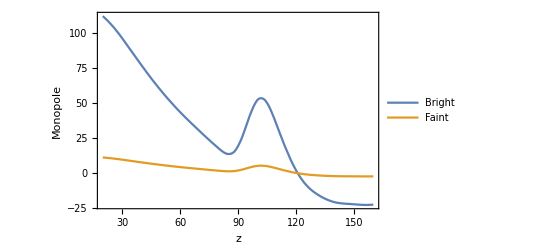

```mathematica
Plot[{d^2MonopoleBf[d],d^2MonopoleFf[d]},{d,20,160},PlotRange->{All,All}, Axes->{True,True},Frame->True,FrameStyle->Directive[Black],LabelStyle->Directive[Black, 12],FrameLabel->{"z",  "Monopole"},RotateLabel->True, ImageSize->{300},PlotLegends->{Bright, Faint}]
```

## Dipole

```mathematica
g1[z_]:=2/(r[z] HH[z])+1/2(-Omm(1+z)+2/(1+z)^2(1-Omm))/HH[z]^2
```

```mathematica
g1zSKA=Table[g1[i],{i,zSKA}]
```

{15.1422,9.64318,7.20087,5.78564,4.84435,4.16406,3.64492,3.23351,2.89842,2.61978,2.3843,2.18266,2.00812,1.85564,1.72137,1.60229,1.49603,1.40068,1.31468}

```mathematica
DipoleΛCDM=evolzSKA HzSKA(3(smodelBzSKA-smodelFzSKA)fzSKA^2 (1/(rH0zSKA HzSKA)-1)- 5(bBzSKA smodelFzSKA-bFzSKA smodelBzSKA)(1/(rH0zSKA HzSKA)-1) fzSKA+(bBzSKA-bFzSKA) g1zSKA fzSKA)
```

{18.5162,7.43904,5.13197,3.08191,2.10902,1.39031,0.928375,0.621277,0.439558,0.354303,0.324656,0.326578,0.346944,0.381092,0.425496,0.478811,0.539924,0.608434,0.682334}

```mathematica
Dipole=(HzSKA/Sigma8z0^2)(3 (βBzSKA-βFzSKA)GtildezSKA^2/5-(bBtildezSKA βFzSKA-bFtildezSKA βBzSKA)GtildezSKA -(bBtildezSKA-bFtildezSKA)(1-2 /(rH0zSKA  HzSKA))GtildezSKA+(3/2)(bBtildezSKA-bFtildezSKA)IhatzSKA-(bBtildezSKA-bFtildezSKA)dGtildezSKA /(H0 HzSKA))
```

{11.7975,4.56608,2.58963,1.67085,1.26591,1.2611,1.41538,1.66727,1.92976,2.12695,2.27262,2.40214,2.53801,2.6847,2.85267,3.03717,3.23845,3.45992,3.6815}

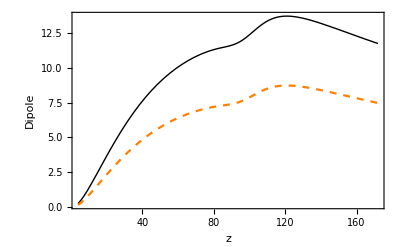

```mathematica
Plot[{d^2DipoleΛCDM[[1]] nu1z0[d],d^2Dipole[[1]] nu1z0[d]},{d,4,172},PlotRange->{All,All}, Axes->{True,True},AxesOrigin->{0,0},PlotStyle->{{Black,Thin},{Orange,Dashed}}, Frame->True,FrameStyle->Directive[Black],LabelStyle->Directive[Black, 12],FrameLabel->{"z",  "Dipole"},RotateLabel->True, ImageSize->{300},PlotLegends-> None]
```

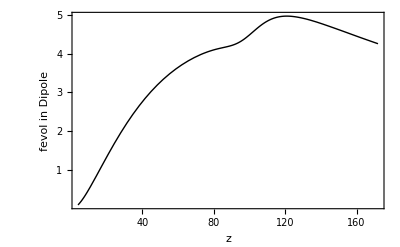

```mathematica
Plot[{d^2DipoleΛCDM[[1]] nu1z0[d]-d^2Dipole[[1]] nu1z0[d]},{d,4,172},PlotRange->{All,All}, Axes->{True,True},AxesOrigin->{0,0},PlotStyle->{{Black,Thin},{Orange,Dashed}}, Frame->True,FrameStyle->Directive[Black],LabelStyle->Directive[Black, 12],FrameLabel->{"z",  "fevol in Dipole"},RotateLabel->True, ImageSize->{300},PlotLegends-> None]
```

```mathematica
Dipolez1[d_]:=Dipole[[1]] nu1z0[d]
```

```mathematica
WideAnglezSKA=-(2/5)(bBtildezSKA-bFtildezSKA)GtildezSKA/(rH0zSKA /H0)
```

{-0.000413473,-0.00024772,-0.000174529,-0.000132663,-0.000105356,-0.0000861054,-0.0000718287,-0.0000608615,-0.0000522159,-0.0000452635,-0.0000395833,-0.0000348813,-0.0000309456,-0.0000276196,-0.0000247851,-0.0000223513,-0.0000202473,-0.0000184172,-0.0000168164}

```mathematica
WideAnglez1[d_]:=WideAnglezSKA[[1]]d mu2z0[d]
```

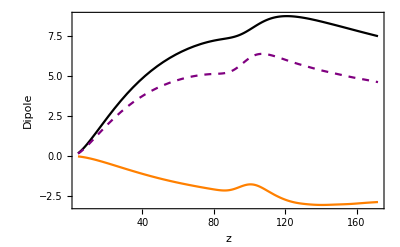

```mathematica
Plot[{d^2Dipole[[1]] nu1z0[d],  d^2(d WideAnglezSKA[[1]] mu2z0[d]),d^2Dipole[[1]] nu1z0[d]+  d^2 (d WideAnglezSKA[[1]] mu2z0[d])},{d,4,172},PlotRange->{All,All}, Axes->{True,True},AxesOrigin->{0,0},PlotStyle->{{Black},{Orange},{Purple,Dashed}}, Frame->True,FrameStyle->Directive[Black],LabelStyle->Directive[Black, 12],FrameLabel->{"z",  "Dipole"},RotateLabel->True, ImageSize->{300},PlotLegends-> None]
```

```mathematica
Table[Dipolez1[d],{d,4,172,4}]
```

{0.0107975,0.0094023,0.00798064,0.00679677,0.00583329,0.00504682,0.0043991,0.00386044,0.00340824,0.00302527,0.00269835,0.00241729,0.00217408,0.00196241,0.00177712,0.00161406,0.00146987,0.00134155,0.00122674,0.00112356,0.00103067,0.000948572,0.000879976,0.000826876,0.00078678,0.000753132,0.000719634,0.000683487,0.000644971,0.000605436,0.000566215,0.000528391,0.000492632,0.000459159,0.000428009,0.000399216,0.000372732,0.000348357,0.00032588,0.000305181,0.000286165,0.000268672,0.000252517}

```mathematica
Table[WideAnglez1[d],{d,4,172,4}]
```

{-0.0012342,-0.0013059,-0.0012503,-0.00116237,-0.00106886,-0.000978758,-0.000895346,-0.000819291,-0.000750624,-0.000688785,-0.000633129,-0.000582991,-0.000537813,-0.000496995,-0.000460269,-0.000426964,-0.000397,-0.000370226,-0.000345888,-0.000323791,-0.000302021,-0.000275096,-0.000239598,-0.000202211,-0.000176272,-0.000168651,-0.000173988,-0.000182219,-0.000187401,-0.00018838,-0.000185463,-0.00017945,-0.000171818,-0.000163693,-0.000155202,-0.000146402,-0.000137865,-0.000130019,-0.000122645,-0.000115436,-0.000108566,-0.00010235,-0.0000967214}

```mathematica
Abs[(Table[Dipolez1[d],{d,4,172,4}]-(Table[Dipolez1[d],{d,4,172,4}]+Table[WideAnglez1[d],{d,4,172,4}]))/(Table[Dipolez1[d],{d,4,172,4}])]
```

{0.114304,0.138891,0.156666,0.171017,0.183235,0.193935,0.203529,0.212227,0.220238,0.227677,0.234636,0.241176,0.247375,0.253258,0.258997,0.264528,0.270092,0.275969,0.281957,0.288182,0.293032,0.290011,0.272278,0.244549,0.224043,0.223932,0.241773,0.266602,0.290558,0.311148,0.327548,0.339616,0.348774,0.356505,0.362614,0.366724,0.369879,0.373235,0.37635,0.378253,0.379381,0.380947,0.383029}

```mathematica
rH0zSKA/H0
```

{433.566,704.263,960.18,1201.58,1428.95,1642.94,1844.3,2033.82,2212.29,2380.49,2539.19,2689.08,2830.84,2965.07,3092.35,3213.19,3328.07,3437.42,3541.64}

## Quadrupole

```mathematica
QuadrupoleBright=-(4 bBtildezSKA GtildezSKA/3 + 4 GtildezSKA^2/7)/Sigma8z0^2
```

{-1.33317,-1.34601,-1.34065,-1.32194,-1.29415,-1.26074,-1.22445,-1.18729,-1.15069,-1.11565,-1.08282,-1.05258,-1.02516,-1.00065,-0.979073,-0.96038,-0.944505,-0.931361,-0.920855}

```mathematica
QuadrupoleFaint=-(4 bFtildezSKA GtildezSKA/3 + 4 GtildezSKA^2/7)/Sigma8z0^2
```

{-0.432359,-0.469356,-0.498577,-0.520948,-0.537646,-0.549884,-0.558777,-0.565293,-0.570228,-0.574218,-0.577764,-0.581248,-0.584966,-0.589141,-0.593941,-0.599495,-0.605904,-0.613245,-0.621582}

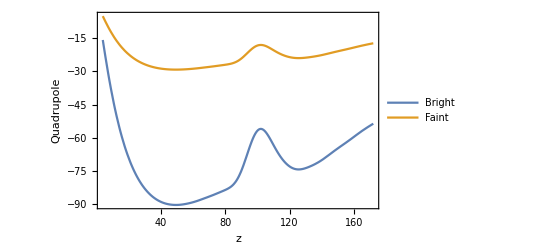

```mathematica
Plot[{d^2 QuadrupoleBright[[1]] mu2z0[d],d^2QuadrupoleFaint [[1]]mu2z0[d]},{d,4,172},PlotRange->{All,All}, Axes->{True,True},AxesOrigin->{0,0},Frame->True,FrameStyle->Directive[Black],LabelStyle->Directive[Black, 12],FrameLabel->{"z",  "Quadrupole"},RotateLabel->True, ImageSize->{300},PlotLegends-> {Bright,Faint}]
```

```mathematica
QuadrupoleBz1[d_]:=QuadrupoleBright[[1]] mu2z0[d]
QuadrupoleFz1[d_]:=QuadrupoleFaint[[1]] mu2z0[d]
```

## Hexadecapole

```mathematica
Hexadecapole=(8 GtildezSKA^2/35)/Sigma8z0^2
```

{0.0723187,0.0761278,0.0779996,0.0782448,0.0772142,0.0752437,0.0726254,0.0695971,0.0663425,0.0629982,0.0596618,0.0564005,0.053258,0.0502613,0.0474248,0.0447544,0.0422501,0.0399079,0.0377213}

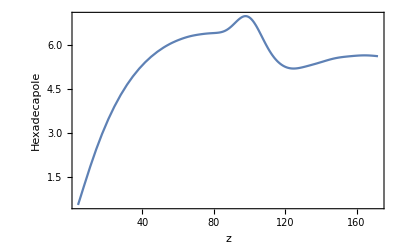

```mathematica
Plot[{d^2Hexadecapole[[1]] mu4z0[d]},{d,4,172},PlotRange->{All,All}, Axes->{True,True},AxesOrigin->{0,0},Frame->True,FrameStyle->Directive[Black],LabelStyle->Directive[Black, 12],FrameLabel->{"z",  "Hexadecapole"},RotateLabel->True, ImageSize->{300},PlotLegends-> None]
```

```mathematica
Hexadecapolez1[d_]:=Hexadecapole[[1]] mu4z0[d];
```

## Octupole

```mathematica
Octupole=(HzSKA/Sigma8z0^2)2 (βBzSKA-βFzSKA)GtildezSKA^2/5
```

{1.39944,0.513119,0.315947,0.212749,0.152646,0.157037,0.184438,0.226418,0.265236,0.285589,0.293283,0.2956,0.297268,0.299041,0.302499,0.306704,0.311523,0.31738,0.321941}

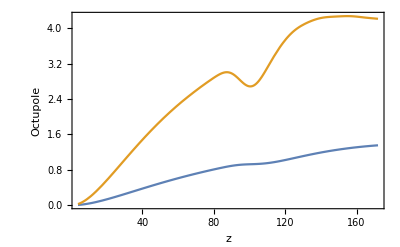

```mathematica
Plot[{d^2 Octupole[[1]] nu3z0[d], d^2 Octupole[[1]] nu3z0[d] - d^2 WideAnglezSKA[[1]]d mu2z0[d]},{d,4,172},PlotRange->{All,All}, Axes->{True,True},AxesOrigin->{0,0},Frame->True,FrameStyle->Directive[Black],LabelStyle->Directive[Black, 12],FrameLabel->{"z",  "Octupole"},RotateLabel->True, ImageSize->{300}]
```

```mathematica
Octupolez1[d_]:=Octupole[[1]] nu3z0[d]
OctupoleWAz1[d_]:=Octupole[[1]] nu3z0[d] -WideAnglezSKA[[1]] d mu2z0[d]
```

## Joint plot

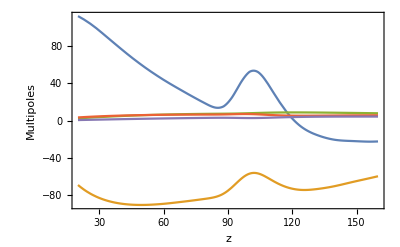

```mathematica
Plot[{d^2 MonopoleBf[d],d^2QuadrupoleBz1[d],d^2Dipolez1[d],d^2Hexadecapolez1[d], d^2 OctupoleWAz1[d]},{d,20,160},PlotRange->{All,All}, Axes->{True,True},Frame->True,FrameStyle->Directive[Black],LabelStyle->Directive[Black, 12],FrameLabel->{"z",  "Multipoles"},RotateLabel->True, ImageSize->{300},PlotLegends-> None]
```

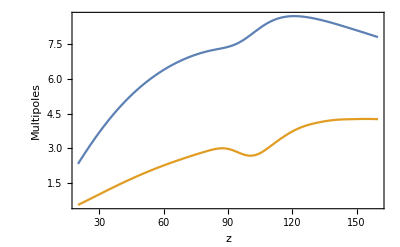

```mathematica
Plot[{d^2Dipolez1[d], d^2 OctupoleWAz1[d]},{d,20,160},PlotRange->{All,All}, Axes->{True,True},Frame->True,FrameStyle->Directive[Black],LabelStyle->Directive[Black, 12],FrameLabel->{"z",  "Multipoles"},RotateLabel->True, ImageSize->{300},PlotLegends-> None]
```

## Signal-to-noise Ratios

```mathematica
{dmin,dmax}
```

{20,160}

```mathematica
{maxsep,ktot,indist,ldist}
```

{40,19,5,36}

## Monopole

```mathematica
ξ0BSKAmatrix=Table[MonopoleBright[[k]]mu0z0[d],{d,dmin,dmax,4},{k,1,ktot}];
Dimensions[ξ0BSKAmatrix]
```

{36,19}

```mathematica
Dimensions[varTOTMONOBrightLp4d4to172zSKA]
```

{19,43,43}

```mathematica
varξ0BTOT=Table[ varTOTMONOBrightLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
```

```mathematica
invcovξ0BTOT=Table[Inverse[varξ0BTOT[[k,All,All]]],{k,1,ktot}];
Dimensions[invcovξ0BTOT]
```

{19,36,36}

```mathematica
ξ0BSKAmatrix[[All,1]]
```

{0.279313,0.185051,0.127321,0.0901498,0.0652434,0.0480381,0.0358549,0.0270538,0.0205795,0.015753,0.0120811,0.00927464,0.00707639,0.0053052,0.00389451,0.0027542,0.00197435,0.00197083,0.00297961,0.00441631,0.00520481,0.00479639,0.00355068,0.00215239,0.000994512,0.000148588,-0.000408935,-0.000731187,-0.000909067,-0.00101177,-0.00105171,-0.00103639,-0.000999138,-0.00096505,-0.000926849,-0.000872619}

```mathematica
SNrSKAMonopole=Table[Sqrt[Sum[ξ0BSKAmatrix[[m,k]] invcovξ0BTOT[[k,m,n]] ξ0BSKAmatrix[[n,k]],{m,1,ldist}, {n,1,ldist}]],{k,1,ktot}]
```

{61.6875,95.9238,125.608,150.46,170.291,185.081,194.638,198.895,197.678,190.895,179.145,162.948,143.204,121.517,98.7065,76.6956,56.81,39.8254,26.4524}

```mathematica
SNSKAMonopoleTotal= Sqrt[Sum[ξ0BSKAmatrix[[m,k]] invcovξ0BTOT[[k,m,n]] ξ0BSKAmatrix[[n,k]], {m,1,ldist}, {n,1,ldist}, {k,1,ktot}]]
```

618.623

## Dipole

```mathematica
ξ1SKAmatrix=Table[(Dipole[[k]])nu1z0[d],{d,dmin,dmax,4},{k,1,ktot}];
Dimensions[ξ1SKAmatrix]
```

{36,19}

```mathematica
varξ1TOT=Table[varTOTDIP2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
```

```mathematica
invcovξ1TOT=Table[Inverse[varξ1TOT[[k,All,All]]],{k,1,ktot}];
Dimensions[invcovξ1TOT]
```

{19,36,36}

```mathematica
SNrSKADipole=Table[Sqrt[Sum[ξ1SKAmatrix[[m,k]] invcovξ1TOT[[k,m,n]] ξ1SKAmatrix[[n,k]],{m,1,ldist}, {n,1,ldist}]],{k,1,ktot}]
```

{43.3584,27.3634,17.5439,11.0154,7.57615,6.66277,6.46335,6.47807,6.27508,5.68751,4.93239,4.16647,3.45808,2.83016,2.271,1.7841,1.36513,1.00741,0.709218}

```mathematica
SNSKADipoleTotal= Sqrt[Sum[ξ1SKAmatrix[[m,k]] invcovξ1TOT[[k,m,n]] ξ1SKAmatrix[[n,k]], {m,1,ldist}, {n,1,ldist}, {k,1,ktot}]]
```

58.2105

```mathematica
1-54.6434/78.2865
```

0.302007

## Dipole + WA

```mathematica
ξ1SKAmatrix=Table[Dipole[[k]]nu1z0[d]+d WideAnglezSKA[[k]] mu2z0[d],{d,dmin,dmax,4},{k,1,ktot}];
Dimensions[ξ1SKAmatrix]
```

{36,19}

```mathematica
varξ1TOT=Table[varTOTDIP2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
```

```mathematica
invcovξ1TOT=Table[Inverse[varξ1TOT[[k,All,All]]],{k,1,ktot}];
Dimensions[invcovξ1TOT]
```

{19,36,36}

```mathematica
SNrSKADipole=Table[Sqrt[Sum[ξ1SKAmatrix[[m,k]] invcovξ1TOT[[k,m,n]] ξ1SKAmatrix[[n,k]],{m,1,ldist}, {n,1,ldist}]],{k,1,ktot}]
```

{35.0917,18.4033,10.0796,5.45417,3.56419,3.72156,4.31553,4.91715,5.14841,4.88102,4.35762,3.75986,3.17321,2.63223,2.13588,1.69343,1.30565,0.969673,0.686204}

```mathematica
SNSKADipoleTotal= Sqrt[Sum[ξ1SKAmatrix[[m,k]] invcovξ1TOT[[k,m,n]] ξ1SKAmatrix[[n,k]], {m,1,ldist}, {n,1,ldist}, {k,1,ktot}]]
```

43.3799

## Quadrupole

```mathematica
ξ2BSKAmatrix=Table[QuadrupoleBright[[k]]mu2z0[d],{d,dmin,dmax,4},{k,1,ktot}];
Dimensions[ξ2BSKAmatrix]
```

{36,19}

```mathematica
varξ2BTOT=Table[varTOTQUADBrightLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
```

```mathematica
invcovξ2BTOT=Table[Inverse[varξ2BTOT[[k,All,All]]],{k,1,ktot}];
Dimensions[invcovξ2BTOT]
```

{19,36,36}

```mathematica
ldist
```

36

```mathematica
SNrSKAQuadrupole=Table[Sqrt[Sum[ξ2BSKAmatrix[[m,k]] invcovξ2BTOT[[k,m,n]] ξ2BSKAmatrix[[n,k]],{m,1,ldist}, {n,1,ldist}]],{k,1,ktot}]
```

{32.4468,52.3884,70.3518,85.5385,97.4076,105.694,110.172,110.817,107.656,100.879,91.2,79.3399,66.2369,53.1044,40.5745,29.5951,20.5755,13.5503,8.46948}

```mathematica
SNSKAQuadrupoleTotal= Sqrt[Sum[ξ2BSKAmatrix[[m,k]] invcovξ2BTOT[[k,m,n]] ξ2BSKAmatrix[[n,k]], {m,1,ldist}, {n,1,ldist}, {k,1,ktot}]]
```

328.524

## Octupole

```mathematica
ξ3SKAmatrix=Table[Octupole[[k]]nu1z0[d],{d,dmin,dmax,4},{k,1,ktot}];
Dimensions[ξ3SKAmatrix]
```

{36,19}

```mathematica
Octupole[[1;;ktot]]
```

{1.39944,0.513119,0.315947,0.212749,0.152646,0.157037,0.184438,0.226418,0.265236,0.285589,0.293283,0.2956,0.297268,0.299041,0.302499,0.306704,0.311523,0.31738,0.321941}

```mathematica
varξ3TOT=Table[varTOTOCT2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
```

```mathematica
invcovξ3TOT=Table[Inverse[varξ3TOT[[k,All,All]]],{k,1,ktot}];
Dimensions[invcovξ3TOT]
```

{19,36,36}

```mathematica
SNrSKAOctupole=Table[Sqrt[Sum[ξ3SKAmatrix[[m,k]] invcovξ3TOT[[k,m,n]] ξ3SKAmatrix[[n,k]],{m,1,ldist}, {n,1,ldist}]],{k,1,ktot}]
```

{6.99435,3.41416,2.17709,1.38294,0.892491,0.807661,0.817089,0.849729,0.827968,0.726875,0.59907,0.475525,0.368685,0.280425,0.20827,0.150802,0.105991,0.0717302,0.0462931}

```mathematica
SNSKAOctupoleTotal= Sqrt[Sum[ξ3SKAmatrix[[m,k]] invcovξ3TOT[[k,m,n]] ξ3SKAmatrix[[n,k]], {m,1,ldist}, {n,1,ldist}, {k,1,ktot}]]
```

8.49507

```mathematica
1-4.68151/8.50621
```

0.449636

## Octupole + WA

```mathematica
ξ3SKAmatrix=Table[Octupole[[k]]nu1z0[d] -d WideAnglezSKA[[k]] mu2z0[d],{d,dmin,dmax,4},{k,1,ktot}];
Dimensions[ξ3SKAmatrix]
```

{36,19}

```mathematica
varξ3TOT=Table[varTOTOCT2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
```

```mathematica
invcovξ3TOT=Table[Inverse[varξ3TOT[[k,All,All]]],{k,1,ktot}];
Dimensions[invcovξ3TOT]
```

{19,36,36}

```mathematica
SNrSKAOctupoleWA=Table[Sqrt[Sum[ξ3SKAmatrix[[m,k]] invcovξ3TOT[[k,m,n]] ξ3SKAmatrix[[n,k]],{m,1,ldist}, {n,1,ldist}]],{k,1,ktot}]
```

{19.4608,13.9752,10.0102,7.02476,4.92987,3.71059,2.90245,2.34632,1.89675,1.48396,1.1324,0.847622,0.624968,0.454853,0.324373,0.226433,0.153974,0.101075,0.0635312}

```mathematica
SNSKAOctupoleWATotal= Sqrt[Sum[ξ3SKAmatrix[[m,k]] invcovξ3TOT[[k,m,n]] ξ3SKAmatrix[[n,k]], {m,1,ldist}, {n,1,ldist}, {k,1,ktot}]]
```

28.0031

## Hexadecapole

```mathematica
ξ4TSKAmatrix=Table[Hexadecapole[[k]]mu4z0[d],{d,dmin,dmax,4},{k,1,ktot}];
Dimensions[ξ4TSKAmatrix]
```

{36,19}

```mathematica
varξ4TTOT=Table[varTOTHEXAtotpopLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
```

```mathematica
invcovξ4TTOT=Table[Inverse[varξ4TTOT[[k,All,All]]],{k,1,ktot}];
Dimensions[invcovξ4TTOT]
```

{19,36,36}

```mathematica
SNrSKAHexadecapole=Table[Sqrt[Sum[ξ4TSKAmatrix[[m,k]] invcovξ4TTOT[[k,m,n]] ξ4TSKAmatrix[[n,k]],{m,1,ldist}, {n,1,ldist}]],{k,1,ktot}]
```

{9.7378,15.1786,19.6006,22.8466,24.8844,25.783,25.6376,24.5914,22.7903,20.396,17.6385,14.7113,11.8091,9.1342,6.76497,4.8075,3.27383,2.12239,1.3088}

```mathematica
SNSKAQuadrupoleTotal= Sqrt[Sum[ξ4TSKAmatrix[[m,k]] invcovξ4TTOT[[k,m,n]] ξ4TSKAmatrix[[n,k]], {m,1,ldist}, {n,1,ldist}, {k,1,ktot}]]
```

74.4918

## Plot

```mathematica
SNSKAz015Dipole=Table[ξ1SKAmatrix[[m,1]]/Sqrt[varξ1TOT[[1,m,m]]],{m,1,ldist}];
SNSKAz015Monopole=Table[ξ0BSKAmatrix[[m,1]]/Sqrt[varξ0BTOT[[1,m,m]]],{m,1,ldist}];
SNSKAz015Quadrupole=Table[Abs[ξ2BSKAmatrix[[m,1]]]/Sqrt[varξ2BTOT[[1,m,m]]],{m,1,ldist}];
SNSKAz015Octupole=Table[Abs[ξ3SKAmatrix[[m,1]]]/Sqrt[varξ3TOT[[1,m,m]]],{m,1,ldist}];
SNSKAz015Hexadecapole=Table[Abs[ξ4TSKAmatrix[[m,1]]]/Sqrt[varξ4TTOT[[1,m,m]]],{m,1,ldist}];
```

```mathematica
ds=Table[d,{d,dmin,dmax,4}];
```

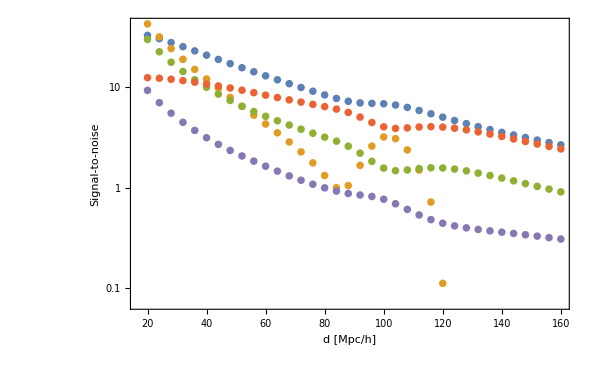

```mathematica
ListLogPlot[{Table[{ds[[i]], SNSKAz015Dipole[[i]]},{i,1,ldist}],Table[{ds[[i]], SNSKAz015Monopole[[i]]},{i,1,ldist}],Table[{ds[[i]], SNSKAz015Quadrupole[[i]]},{i,1,ldist}], Table[{ds[[i]], SNSKAz015Octupole[[i]]},{i,1,ldist}],
Table[{ds[[i]], SNSKAz015Hexadecapole[[i]]},{i,1,ldist}]},PlotRange->Full,PlotStyle->{•},Axes->{False,False},Frame->True,FrameStyle->Directive[Black],LabelStyle->Directive[Black, 12],FrameLabel->{"d [Mpc/h]","Signal-to-noise"},RotateLabel->True]
```

# Export

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/danielsb/Documents/GitHub/magevolbias/Covariance

```mathematica
SetDirectory["multi_split"]
```

/Users/danielsb/Documents/GitHub/magevolbias/Covariance/multi_split

```mathematica
(*Export["CovarianceMatrixzSKA_d"<>ToString[distances[[indist]]]<>"to"<>ToString[distances[[maxsep]]]<>".txt",CovMatrixtabzSKA,"Table","FieldSeparators"->" ",OverwriteTarget->"KeepBoth"]*)
```

```mathematica
(*Export["CovarianceMatrix_P_at_z"<>ToString[zSKA[[1]]]<>"_d"<>ToString[distances[[indist]]]<>"to"<>ToString[distances[[maxsep]]]<>".txt",CovMatrixtabzSKA[[1]],"Table","FieldSeparators"->" ",OverwriteTarget->True]*)
```

```mathematica
nBSKA
```

1/5

```mathematica
nFSKA
```

4/5

```mathematica
For[i=1,i<= Length[zSKA],i++,
Export["CovarianceMatrix_at_z"<>ToString[zSKA[[i]]]<>"_d"<>ToString[distances[[indist]]]<>"to"<>ToString[distances[[maxsep]]]<>"_msplit-"<>StringReplace[ToString[Round[100 N[nBSKA]], InputForm],"/"->"-"]<>"B_"<>StringReplace[ToString[Round[100N[nFSKA]], InputForm],"/"->"-"]<>"F.txt",CovMatrixtabzSKA[[i]],"Table","FieldSeparators"->" ",OverwriteTarget->True]]
```

EXPORT - WITH OCTUPOLE

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/danielsb/Documents/GitHub/magevolbias/Covariance

```mathematica
SetDirectory["octupole"]
```

/Users/danielsb/Documents/GitHub/magevolbias/Covariance/octupole

```mathematica
For[i=1,i<= Length[zSKA],i++,
Export["CovarianceMatrixOCT_at_z"<>ToString[zSKA[[i]]]<>"_d"<>ToString[distances[[indist]]]<>"to"<>ToString[distances[[maxsep]]]<>"_msplit-"<>StringReplace[ToString[Round[100 N[nBSKA]], InputForm],"/"->"-"]<>"B_"<>StringReplace[ToString[Round[100N[nFSKA]], InputForm],"/"->"-"]<>"F.txt",CovMatrixOCTtabzSKA[[i]],"Table","FieldSeparators"->" ",OverwriteTarget->True]]
```

```mathematica
nBSKA
```

1/5

```mathematica
nFSKA
```

4/5

```mathematica
Exit[]
```